# 知識構造化法

Update: 20131203

2013年度　秋学期、筑波大学　学部3・4年次、5・6限

## 1.知識構造化とは

[講義室]

### 知識構造化法ガイダンス

「知識」も「構造」も明確な定義はなく、「知識構造化」もなんだかよくわからないが、知識を構造化することについては、大きく次の二つの考えがある:

1. 知識を構造化するための形式記述をどのように定義すればよいかという問題

2. 単なるデータの寄せ集めから、あるいは既存の知識からどのように新しい知識を発見するかという問題

ここでは、おもに2について、「探索的データ解析」を中心に学ぶ。 -> [4.探索的データ解析]

ある程度の理論の解説もありますが、Mathematica等を利用して実践的な解析ができる技術を身につけるための授業です。習熟度に応じLinux上でC言語も使用します。
なんらかのプログラミング経験があることが望ましいですが、初心者に対しても丁寧に指導します。
授業方針に対するリクエストは歓迎です。

履修者確認

希望調査等

プログラミング言語の経験 -> Ruby

出席 -> とらない

期末試験 -> 行なわない

レポートあり

授業中の回答で加点

### 知識構造化とは

スライド: 知識構造化法_中山先生/知識構造化法1.pptx

表現の変換・解釈 
図やチャートを用いて情報や思考を分かりやすく示す

構造の付加(メタデータの付与)
スライド:知識構造化法_中山先生/知識構造化法1-2.pptx

尺度水準
スライド:知識構造化法_中山先生/知識構造化法1-2.pptx

[実習室]

腕試し 
フィボナッチ数列の第n項を求める関数のプログラム(再帰)

R

Mathematica

2013/10/03

## 2.データの構造について

まずはデータの話。Mathematicaの利用について体系的に学ぶのは次の単元から。

Mathematicaによるフィボナッチ数列のプログラムは後ほど。

### データとは

処理系が扱える表現全てがデータである。

ちなみに: 演算装置内の処理を考えるとき、「instruction」と「data」に分けて考える。ここでの「data」は別の概念と捉えたほうがよいであろう。

### データ処理とは

スライド: turing.odp

データ処理とは、処理対象と処理命令の定義が記述された表現を、その表現以外の知識(ルール)を用い、表現が変化しなくなるまで評価を続けることである(べつの言葉で言えば、表現評価系を用いた表現の変換)。処理対象と処理命令は、分離が曖昧であり広い意味ではすべて処理対象である。

「計算機」と「データ」を抽象化するとチューリングマシンの概念となる。「人間からの割り込みを許すチューリングマシン」の実装が「計算機」である。

#### チューリングマシン

スライド: turing.odp

```mathematica
??TuringMachine
```

RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定されたルールで初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ進んだチューリングマシンの進化を表すリストを生成する． 
RowBox[{"TuringMachine", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] StyleBox["init", "TI"] を1ステップ進化させた結果を与える．

Attributes[TuringMachine]={Protected,ReadProtected}

```mathematica
??IntegerDigits
```

RowBox[{"IntegerDigits", "[", StyleBox["n", "TI"], "]"}] 十進数表記における整数 StyleBox["n", "TI"] の桁数字をリスト形式で返す．
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"]}], "]"}] StyleBox["b", "TI"] 進数における桁数字を整数 StyleBox["n", "TI"] のリストで返す．
RowBox[{"IntegerDigits", "[", RowBox[{StyleBox["n", "TI"], ",", StyleBox["b", "TI"], ",", StyleBox["len", "TI"]}], "]"}] この書式を使うと，リスト長が StyleBox["len", "TI"] になるよう出力されるリストの左側にゼロが付け足される．

Attributes[IntegerDigits]={Listable,Protected}

```mathematica
IntegerDigits[2506,2]
```

{1,0,0,1,1,1,0,0,1,0,1,0}

```mathematica
??FromDigits
```

RowBox[{"FromDigits", "[", StyleBox["list", "TI"], "]"}] 十進法の桁数字からなるリストから単一整数を構築する．
RowBox[{"FromDigits", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["b", "TI"]}], "]"}] StyleBox["b", "TI"] を底とする桁数字を使う．
RowBox[{"FromDigits", "[", StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], "]"}] 桁数字の列から単一整数を構築する．
RowBox[{"FromDigits", "[", RowBox[{StyleBox["\"\!\(\*StyleBox[\"string\",\"TI\"]\)\"", ShowStringCharacters->True], ",", StyleBox["\"Roman\"",ShowStringCharacters->True]}], "]"}] ローマ数字から整数を構築する．

Attributes[FromDigits]={Protected}

```mathematica
FromDigits[{1,0,0,1,1,1,0,0,1,0,1,0},2]
```

2506

```mathematica
turingCurrentState[s_,k_]:=Module[
{sets,setk,current},
sets=Range[0,s-1];
setk=Range[0,k-1];
current=Flatten[Outer[List,sets,setk],1]
]
```

```mathematica
turingAllRules[s_,k_]:=Module[
{(*numrule,*)numStateSet,numOperateSet,sets,setk,(*current,*)selections,next},
(*numrule=(2 s k)^(s k);*)
numStateSet=s k;
numOperateSet=2 s k;
sets=Range[0,s-1];
setk=Range[0,k-1];
selections=Tuples[Range[numOperateSet],numStateSet];
next=Flatten[Outer[List,sets,setk,{"L","R"}],2];
Map[next[[#]]&,selections]
]
```

#### セルオートマトン

```mathematica
??CellularAutomaton
```

RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", StyleBox["t", "TI"]}], "]"}] 指定した条件でセルオートマトンを初期条件 StyleBox["init", "TI"] から StyleBox["t", "TI"] ステップ実行した進化を表すリストを生成する．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"]}], "]"}] 1ステップ分の StyleBox["init", "TI"] の進化の結果を返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["tspec", "TI"], ",", StyleBox["xspec", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["tspec", "TI"]，StyleBox[RowBox[{"xspec", " "}], "TI"]等で指定された進化の部分だけを返す．
RowBox[{"CellularAutomaton", "[", RowBox[{StyleBox["rule", "TI"], ",", StyleBox["init", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["t", "TI"], ",", "All", ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] StyleBox["t", "TI"] ステップの間に影響を受けるであろうすべてのセルを各ステップに含む．

Attributes[CellularAutomaton]={Protected}

```mathematica
FromDigits[{0,0,0,1,0,0,0,1},2]
```

17

```mathematica
numRuleToCellList[n_,d_]:=(* n: 第nルール、d: d次元 *)
Module[{dig,stats,box,bbox,cellstat},
dig=3^d;
stats=2^dig;
bbox=Reverse[Map[IntegerDigits[#,2,dig]&,Range[0,stats-1]]];
cellstat=IntegerDigits[n,2,stats];
Transpose[{bbox,cellstat}]
]
```

```mathematica
cellListVis1D[rule_]:=Grid[{Map[Grid[{#[[1]],{Null,#[[2]],Null}},Frame->All]&,rule]}]
```

1近傍、1次元、第0ルール

```mathematica
cellListVis1D[numRuleToCellList[2,1]]
```

1 | 1 | 1
 | 0 |  | 1 | 1 | 0
 | 0 |  | 1 | 0 | 1
 | 0 |  | 1 | 0 | 0
 | 0 |  | 0 | 1 | 1
 | 0 |  | 0 | 1 | 0
 | 0 |  | 0 | 0 | 1
 | 1 |  | 0 | 0 | 0
 | 0 |

#### ラムダ計算(今期やらない)

### プログラミング言語とは

広義には、人間が計算機へ指示を伝えるための言語であるが、これではさまざまな仕組みがプログラミング言語になってしまう。

そこで、狭義には、その中でも以下を満たすものであると考える。

効率的にデータ処理を行うためにコンパイラ(インタープリタ)が対応すべき表現 :

抽象化(変数)
 ポインタもアドレスを格納する変数に過ぎない。

繰り返し(または再帰)
    再帰表現と繰り返し表現は可換であるが、書き直しの手間がかかるため、双方備えるべき。

条件分岐

### データ型

ほとんどすべてのプログラミング言語では、データ型が定義されている。

主な型:

- 整数(Integer)

- 浮動小数(Real)

- 複素数(Complex)

- ブール代数

- 文字

- ポインタ

主な上位構造:

- 配列

- 構造体

- 列挙型

Mathematicaの場合、式はリストであり、頭部の情報にデータ型を含む。関数Head[]によって返されるオブジェクトである。関数にHead[]を適応すると、返される値は関数名である。

```mathematica
Head[a]
```

Symbol

```mathematica
Head[6]
```

Integer

```mathematica
Head[6.]
```

Real

```mathematica
Head[1-I]
```

Complex

```mathematica
Head["AAA"]
```

String

```mathematica
Head[fib]
```

Symbol

Headをネストさせて作用させると最終的にSymbolが得られる

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
Head[f[][][]]//Head
```

f[]

```mathematica
Head[f[][][]]//Head//Head
```

f

```mathematica
Head[f[][][]]//Head//Head//Head
```

Symbol

```mathematica
Head[f[][][]]//Head//Head//Head//Head
```

Symbol

```mathematica
Head[6]//Head
```

Symbol

#### リスト(Mathematicaではリストもツリーで表される)

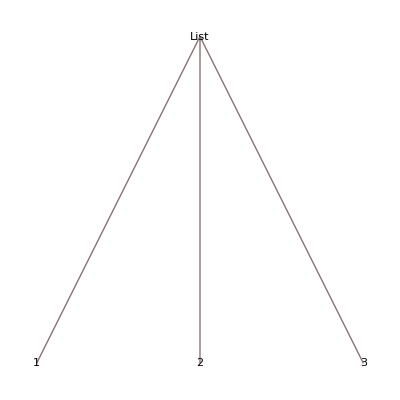

```mathematica
TreeForm[{1,2,3}]
```

#### ツリー

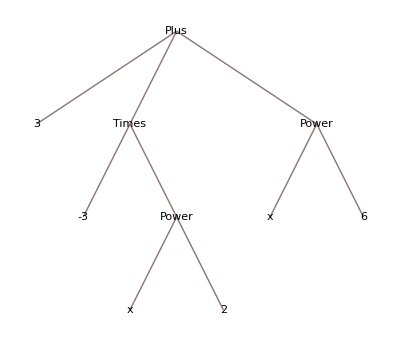

```mathematica
TreeForm[x^6-3x^2+3]
```

```mathematica
TreeForm[7^6-7*8+2]
```

-Graphics-

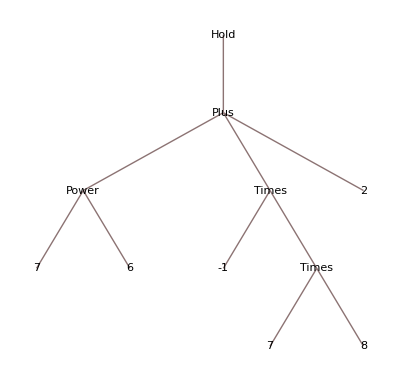

```mathematica
TreeForm[Hold[7^6-7*8+2]]
```

#### グラフ

リストでグラフは直接表現できないので、 Graph[]という予約済み関数を使う。

```mathematica
??Graph
```

RowBox[{"Graph", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] 辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{StyleBox["{", "TI"], RowBox[{StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["1", "TR"]], "TI"], ",", StyleBox[SubscriptBox[StyleBox["v", "TI"], StyleBox["2", "TR"]], "TI"], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}], ",", RowBox[{StyleBox["{", "TI"], RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], StyleBox["}", "TI"]}]}], "]"}] 頂点 SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]]，辺 SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]]のグラフを与える．
RowBox[{"Graph", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["i", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["v", "TI"], StyleBox["i", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["…", "TR"], ",", RowBox[{SubscriptBox[StyleBox["w", "TI"], StyleBox["j", "TI"]], "[", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["j", "TI"]], ",", StyleBox["…", "TR"]}], "]"}], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 頂点と辺の特性が記号ラッパー SubscriptBox[StyleBox["w", "TI"], StyleBox["k", "TI"]]で定義されているグラフを与える．

Attributes[Graph]={NHoldAll,Protected}
 
Options[Graph]={AlignmentPoint→Center,AspectRatio→Automatic,Axes→False,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ContentSelectable→Automatic,DirectedEdges→Automatic,EdgeCapacity→Automatic,EdgeCost→Automatic,EdgeLabels→Automatic,EdgeLabelStyle→Automatic,EdgeShapeFunction→Automatic,EdgeStyle→Automatic,EdgeWeight→Automatic,Editable→False,Epilog→{},Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→None,FrameTicksStyle→{},GraphHighlight→{},GraphHighlightStyle→Automatic,GraphLayout→Automatic,GraphRoot→Automatic,GraphStyle→Automatic,GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotRange→All,PlotRangeClipping→False,PlotRangePadding→Automatic,PlotRegion→Automatic,Prolog→{},Properties→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{},VertexCapacity→Automatic,VertexCoordinates→Automatic,VertexLabels→Automatic,VertexLabelStyle→Automatic,VertexShape→Automatic,VertexShapeFunction→Automatic,VertexSize→Automatic,VertexStyle→Automatic,VertexWeight→Automatic}

#### 構造体

Mathematicaに構造体はない。かわりにリストを入れ子(ツリー)にして表現する。

```mathematica
x={1,2,2,{1,2,{1}}}
```

{1,2,2,{1,2,{1}}}

```mathematica
x
```

{1,2,2,{1,2,{1}}}

#### ポインタ

Mathematicaでのポインタは単に変数となる。

従って、変数に対し再帰定義もできる。

```mathematica
y=.
y={1,2,y}
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

ちゃんと、yには再帰構造が定義されている。

```mathematica
y
```

$RecursionLimit::reclim: 最大再帰回数1024を超えています．

{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{1,2,{MaxFormatDepthExceeded}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}}

### フィボナッチ数列ふたたび

```mathematica
fib[n_]:=If[n==1,1,If[n==2,1,fib[n-1]+fib[n-2]]]
```

```mathematica
fib[6]
```

8

Mathematicaでは、特定の引数をとる場合の関数に、直接値を代入できる。

```mathematica
fi[0]:=0
fi[1]:=1
fi[n_]:=fi[n-1]+fi[n-2]
```

```mathematica
fi[10]
```

55

以下は階乗の例。

```mathematica
fa[0]:=1
fa[n_]:=n fa[n-1]
```

```mathematica
fa[0]
```

1

```mathematica
fa[6]
```

720

```mathematica
0!
```

1

```mathematica
6!
```

720

2013/10/10

2013/10/17 は休講

### 巨大な知識構造化の例

Wolfram Alpha(スライド: turing.odp)

Sematitic web

XML

RDF: XMLの拡張として実装されている

トリプル: RDFにおける基礎的な構造: E-Rモデル

### いままでは、計算機上にある情報(データ)を扱う話。では、機械可読でない情報を計算機で扱うには?

センサーを使う(センサーと接続可能な場合)。または、解析器付きセンサーが出力するデータを読み込む。

Linuxにおける /dev/mouse からの信号の例

オシロスコープの例(実演) : 
4-5人のグループをつくり、グループごとにデータをとる。他のグループは下の課題をおこなう。すべてのグループがデータを取り終わったら、終了。

### 提出課題(2)

1. 第1、2、3項を定義し、一般項を前3項を参照する漸化式として定義することにより、数列を定義せよ

2. 1の数列の第50項を求めよ

## 2.5.Mathematicaことはじめ(NEW)

Mathematicaの言語構造は、一貫してリスト型である。リスト構造であれば直接扱うことができる。リストより高次の構造は、予約済み関数がサポートする。

### すべては関数である

Mathematicaは、すべての表現を関数としてとらえる。

関数の形式は、関数名[引数...]である。数値や文字(列)は、引数をとらない特別な関数(名)として解釈できる。

```mathematica
1+1
```

2

1 は関数か?

```mathematica
1[1]
```

1[1]

怒られない。

```mathematica
1[x_]:=x^2
```

SetDelayed::write: 1[x_]のタグIntegerはProtectedです．

$Failed

が、プロテクトされている。

つまり、関数表現を禁止しない代わりに、関数名に対するユーザー定義を禁止し、特別な関数名として解釈できる無限の関数集合を定義している。

```mathematica
1[1]-1[1]
```

0

```mathematica
(2[1]-1)^2//Expand
```

1-2 2[1]+(2[1])^2

```mathematica
"y"+"y"
```

2 y

可能な限り、群や環の性質を持たせてある。

### 代入

変数の代入

```mathematica
i=1
```

1

```mathematica
i
```

1

```mathematica
Set[j,2]
```

2

```mathematica
j
```

2

関数の代入(定義)

```mathematica
f[x_]:=x^2
```

```mathematica
f[4]
```

16

```mathematica
SetDelayed[g[x_],x^3]
```

```mathematica
g[4]
```

64

### 繰り返し

単純繰り返し

```mathematica
For[i=0,i<5,i++,i]
```

```mathematica
i
```

5

繰り返しによる配列作成

```mathematica
Table[i,{i,5}]
```

{1,2,3,4,5}

繰り返しによる配列作成 (変数)

```mathematica
matc=Array[c,{2,3}]
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],c[2,2],c[2,3]}}

```mathematica
c[2,2]=5
```

5

```mathematica
matc
```

{{c[1,1],c[1,2],c[1,3]},{c[2,1],5,c[2,3]}}

関数の繰り返し適応

```mathematica
Nest[Function[#+1],0,5]
```

5

### 条件分岐

```mathematica
i
```

5

```mathematica
If[i<5,0,10]
```

10

### 純関数

無名関数とも言う。

普通の関数定義

```mathematica
f[x_,y_]:=x+y
```

純関数の定義

```mathematica
Function[#1+#2](*定義のみ、#1は1番目の引数、#2は2番目の引数*)
```

#1+#2&

```mathematica
Function[#1 + #2][1,2](*定義と同時に使う、これが純関数の一般的な使い方*)
```

3

```mathematica
Function[{x,y},x+y][1, 2](*引数には#でなく任意の名前を付けることができる*)
```

3

Function[{x, y}, x + y][1, 2]のうちで、Function[{x,y},x+y]部分が頭部となる。

```mathematica
Head[f[][][]]
```

f[][]

```mathematica
g=Function[#1+#2](*定義を代入*)
```

#1+#2&

```mathematica
g[1,2](*関数gとして使える*)
```

3

```mathematica
h[3,2]/.{h->Function[#1 #2]}(*一時的にhに関数を割り当てる*)
```

6

```mathematica
h[3,2]
```

h[3,2]

```mathematica
h[][3,2]/.{h[]->Function[#1 #2]}
```

6

```mathematica
h[][3,2]/.{h[]->Function[{x,y},x y]}
```

6

### 微分記号 ‘ (ダッシュ)と微分関数D

```mathematica
FullForm[f']
```

Derivative[1][f]

```mathematica
j[x_]:=x^3
```

```mathematica
j' (*j'そのものが関数として使える*)
```

3 #1^2&

```mathematica
FullForm[j']
```

Function[Times[3,Power[Slot[1],2]]]

```mathematica
j'[g]
```

3 g^2

```mathematica
Derivative[1][j][x]
```

3 x^2

Derivativeを使って直接微分する:

```mathematica
Derivative[1][x^3][x] (*jの代わりにx^3では微分しない -> 関数として定義されている、つまりポインタである必要がある*)
```

(x^3)'[x]

```mathematica
Function[u, u^3][x]
```

x^3

```mathematica
Derivative[1][Function[u,u^3]][x](*そこで、純関数を使う*)
```

3 x^2

```mathematica
Derivative[1][Function[u,j[u]]][x]
```

3 x^2

```mathematica
Derivative[1][Function[x,x^3]][x]
```

3 x^2

Dを使って直接微分する

```mathematica
D[x^3,x]
```

3 x^2

### 構造生成、構造処理、構造テスト、構造アクセス

```mathematica
t1=Table[{i,j},{i,3},{j,4}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}

```mathematica
Dimensions[{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}}}]
```

{3,4,2}

```mathematica
ft1=Map[f[#]&,t1]
```

{{{1,1},{1,4},{1,9},{1,16}},{{4,1},{4,4},{4,9},{4,16}},{{9,1},{9,4},{9,9},{9,16}}}

```mathematica
Dimensions[{{{1,1},{1,4},{1,9},{1,16}},{{4,1},{4,4},{4,9},{4,16}},{{9,1},{9,4},{9,9},{9,16}}}]
```

{3,4,2}

```mathematica
Map[g,t1]
```

{{{1,1},{1,8},{1,27},{1,64}},{{8,1},{8,8},{8,27},{8,64}},{{27,1},{27,8},{27,27},{27,64}}}

```mathematica
Dimensions[Map[g,t1]]
```

{3,4,2}

```mathematica
Map[g,t1,{1}]
```

{{{1,1},{1,8},{1,27},{1,64}},{{8,1},{8,8},{8,27},{8,64}},{{27,1},{27,8},{27,27},{27,64}}}

```mathematica
Map[g,t1,{-1}]
```

{{{1,1},{1,8},{1,27},{1,64}},{{8,1},{8,8},{8,27},{8,64}},{{27,1},{27,8},{27,27},{27,64}}}

```mathematica
Dimensions[Map[g,t1,{-1}]]
```

{3,4,2}

```mathematica
tft1=Outer[List,t1,ft1]
```

{{{{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}},{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}}},{{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}},{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}}},{{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}},{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}}},{{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}},{{{{4,1},{4,1}},{{4,1},{4,4}},{{4,1},{4,9}},{{4,1},{4,16}}},{{{4,4},{4,1}},{{4,4},{4,4}},{{4,4},{4,9}},{{4,4},{4,16}}},{{{4,9},{4,1}},{{4,9},{4,4}},{{4,9},{4,9}},{{4,9},{4,16}}}}}},{{{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}},{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}}},{{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}},{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}}},{{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}},{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}}},{{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}},{{{{4,1},{4,1}},{{4,1},{4,4}},{{4,1},{4,9}},{{4,1},{4,16}}},{{{4,4},{4,1}},{{4,4},{4,4}},{{4,4},{4,9}},{{4,4},{4,16}}},{{{4,9},{4,1}},{{4,9},{4,4}},{{4,9},{4,9}},{{4,9},{4,16}}}}}},{{{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}},{{{{1,1},{1,1}},{{1,1},{1,4}},{{1,1},{1,9}},{{1,1},{1,16}}},{{{1,4},{1,1}},{{1,4},{1,4}},{{1,4},{1,9}},{{1,4},{1,16}}},{{{1,9},{1,1}},{{1,9},{1,4}},{{1,9},{1,9}},{{1,9},{1,16}}}}},{{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}},{{{{2,1},{2,1}},{{2,1},{2,4}},{{2,1},{2,9}},{{2,1},{2,16}}},{{{2,4},{2,1}},{{2,4},{2,4}},{{2,4},{2,9}},{{2,4},{2,16}}},{{{2,9},{2,1}},{{2,9},{2,4}},{{2,9},{2,9}},{{2,9},{2,16}}}}},{{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}},{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}}},{{{{{3,1},{3,1}},{{3,1},{3,4}},{{3,1},{3,9}},{{3,1},{3,16}}},{{{3,4},{3,1}},{{3,4},{3,4}},{{3,4},{3,9}},{{3,4},{3,16}}},{{{3,9},{3,1}},{{3,9},{3,4}},{{3,9},{3,9}},{{3,9},{3,16}}}},{{{{4,1},{4,1}},{{4,1},{4,4}},{{4,1},{4,9}},{{4,1},{4,16}}},{{{4,4},{4,1}},{{4,4},{4,4}},{{4,4},{4,9}},{{4,4},{4,16}}},{{{4,9},{4,1}},{{4,9},{4,4}},{{4,9},{4,9}},{{4,9},{4,16}}}}}}}

```mathematica
Dimensions[tft1]
```

{3,4,2,3,4,2,2}

```mathematica
Depth[tft1]
```

8

Depth[]はテンソルのランク+1を返す。あるいは、ツリーの深さを返す。

```mathematica
Depth[123]
```

1

TensorRank[]も使える。

```mathematica
TensorRank[{{2,1},{3,4}}]
```

2

```mathematica
TensorRank[{{2,1,{2}},{3,4,{2}}}]
```

2

内積

```mathematica
Inner[List,{1,2,3},{4,5,6},List]
```

{{1,4},{2,5},{3,6}}

```mathematica
Inner[Times,{1,2,3},{4,5,6},List]
```

{4,10,18}

```mathematica
Inner[Times,{1,2,3},{4,5,6},Plus]
```

32

```mathematica
tft1=Inner[List,t1,ft1,List,1]
```

{{{{{{1,1},{2,4},{3,9}},{{1,1},{2,1},{3,1}}},{{{1,1},{2,4},{3,9}},{{1,4},{2,4},{3,4}}},{{{1,1},{2,4},{3,9}},{{1,9},{2,9},{3,9}}},{{{1,1},{2,4},{3,9}},{{1,16},{2,16},{3,16}}}},{{{{1,1},{1,4},{1,9}},{{1,1},{1,1},{1,1}}},{{{1,1},{1,4},{1,9}},{{1,4},{1,4},{1,4}}},{{{1,1},{1,4},{1,9}},{{1,9},{1,9},{1,9}}},{{{1,1},{1,4},{1,9}},{{1,16},{1,16},{1,16}}}}},{{{{{1,1},{2,4},{3,9}},{{1,1},{2,1},{3,1}}},{{{1,1},{2,4},{3,9}},{{1,4},{2,4},{3,4}}},{{{1,1},{2,4},{3,9}},{{1,9},{2,9},{3,9}}},{{{1,1},{2,4},{3,9}},{{1,16},{2,16},{3,16}}}},{{{{2,1},{2,4},{2,9}},{{2,1},{2,1},{2,1}}},{{{2,1},{2,4},{2,9}},{{2,4},{2,4},{2,4}}},{{{2,1},{2,4},{2,9}},{{2,9},{2,9},{2,9}}},{{{2,1},{2,4},{2,9}},{{2,16},{2,16},{2,16}}}}},{{{{{1,1},{2,4},{3,9}},{{1,1},{2,1},{3,1}}},{{{1,1},{2,4},{3,9}},{{1,4},{2,4},{3,4}}},{{{1,1},{2,4},{3,9}},{{1,9},{2,9},{3,9}}},{{{1,1},{2,4},{3,9}},{{1,16},{2,16},{3,16}}}},{{{{3,1},{3,4},{3,9}},{{3,1},{3,1},{3,1}}},{{{3,1},{3,4},{3,9}},{{3,4},{3,4},{3,4}}},{{{3,1},{3,4},{3,9}},{{3,9},{3,9},{3,9}}},{{{3,1},{3,4},{3,9}},{{3,16},{3,16},{3,16}}}}},{{{{{1,1},{2,4},{3,9}},{{1,1},{2,1},{3,1}}},{{{1,1},{2,4},{3,9}},{{1,4},{2,4},{3,4}}},{{{1,1},{2,4},{3,9}},{{1,9},{2,9},{3,9}}},{{{1,1},{2,4},{3,9}},{{1,16},{2,16},{3,16}}}},{{{{4,1},{4,4},{4,9}},{{4,1},{4,1},{4,1}}},{{{4,1},{4,4},{4,9}},{{4,4},{4,4},{4,4}}},{{{4,1},{4,4},{4,9}},{{4,9},{4,9},{4,9}}},{{{4,1},{4,4},{4,9}},{{4,16},{4,16},{4,16}}}}}}

```mathematica
Dimensions[tft1]
```

{4,2,4,2,3,2}

```mathematica
tft1T=Inner[Times,t1,ft1,List,1]
```

{{{{{1,8,27},{1,2,3}},{{1,8,27},{4,8,12}},{{1,8,27},{9,18,27}},{{1,8,27},{16,32,48}}},{{{1,4,9},{1,1,1}},{{1,4,9},{4,4,4}},{{1,4,9},{9,9,9}},{{1,4,9},{16,16,16}}}},{{{{1,8,27},{1,2,3}},{{1,8,27},{4,8,12}},{{1,8,27},{9,18,27}},{{1,8,27},{16,32,48}}},{{{2,8,18},{2,2,2}},{{2,8,18},{8,8,8}},{{2,8,18},{18,18,18}},{{2,8,18},{32,32,32}}}},{{{{1,8,27},{1,2,3}},{{1,8,27},{4,8,12}},{{1,8,27},{9,18,27}},{{1,8,27},{16,32,48}}},{{{3,12,27},{3,3,3}},{{3,12,27},{12,12,12}},{{3,12,27},{27,27,27}},{{3,12,27},{48,48,48}}}},{{{{1,8,27},{1,2,3}},{{1,8,27},{4,8,12}},{{1,8,27},{9,18,27}},{{1,8,27},{16,32,48}}},{{{4,16,36},{4,4,4}},{{4,16,36},{16,16,16}},{{4,16,36},{36,36,36}},{{4,16,36},{64,64,64}}}}}

```mathematica
Dimensions[tft1T]
```

{4,2,4,2,3}

```mathematica
tft1C=Inner[Times,t1,ft1,Tr,1]
```

{{{{Tr[1,8,27],Tr[1,2,3]},{Tr[1,8,27],Tr[4,8,12]},{Tr[1,8,27],Tr[9,18,27]},{Tr[1,8,27],Tr[16,32,48]}},{{Tr[1,4,9],Tr[1,1,1]},{Tr[1,4,9],Tr[4,4,4]},{Tr[1,4,9],Tr[9,9,9]},{Tr[1,4,9],Tr[16,16,16]}}},{{{Tr[1,8,27],Tr[1,2,3]},{Tr[1,8,27],Tr[4,8,12]},{Tr[1,8,27],Tr[9,18,27]},{Tr[1,8,27],Tr[16,32,48]}},{{Tr[2,8,18],Tr[2,2,2]},{Tr[2,8,18],Tr[8,8,8]},{Tr[2,8,18],Tr[18,18,18]},{Tr[2,8,18],Tr[32,32,32]}}},{{{Tr[1,8,27],Tr[1,2,3]},{Tr[1,8,27],Tr[4,8,12]},{Tr[1,8,27],Tr[9,18,27]},{Tr[1,8,27],Tr[16,32,48]}},{{Tr[3,12,27],Tr[3,3,3]},{Tr[3,12,27],Tr[12,12,12]},{Tr[3,12,27],Tr[27,27,27]},{Tr[3,12,27],Tr[48,48,48]}}},{{{Tr[1,8,27],Tr[1,2,3]},{Tr[1,8,27],Tr[4,8,12]},{Tr[1,8,27],Tr[9,18,27]},{Tr[1,8,27],Tr[16,32,48]}},{{Tr[4,16,36],Tr[4,4,4]},{Tr[4,16,36],Tr[16,16,16]},{Tr[4,16,36],Tr[36,36,36]},{Tr[4,16,36],Tr[64,64,64]}}}}

```mathematica
tft1C=Inner[Times,t1,ft1,Function[Tr[{##}]],1]
```

{{{{36,6},{36,24},{36,54},{36,96}},{{14,3},{14,12},{14,27},{14,48}}},{{{36,6},{36,24},{36,54},{36,96}},{{28,6},{28,24},{28,54},{28,96}}},{{{36,6},{36,24},{36,54},{36,96}},{{42,9},{42,36},{42,81},{42,144}}},{{{36,6},{36,24},{36,54},{36,96}},{{56,12},{56,48},{56,108},{56,192}}}}

```mathematica
Dimensions[tft1C]
```

{4,2,4,2}

外積

```mathematica
Outer[List,{1,2,3},{4,5,6}]
```

{{{1,4},{1,5},{1,6}},{{2,4},{2,5},{2,6}},{{3,4},{3,5},{3,6}}}

高次元データへのアクセス

```mathematica
tft1C[[1,1,1,1]]
```

1

```mathematica
tft1C[[1,1,1,1]]=10
```

10

```mathematica
tft1C
```

{{{{10,1},{1,4},{1,9},{1,16}},{{1,1},{1,4},{1,9},{1,16}}},{{{1,1},{1,4},{1,9},{1,16}},{{2,2},{2,8},{2,18},{2,32}}},{{{1,1},{1,4},{1,9},{1,16}},{{3,3},{3,12},{3,27},{3,48}}},{{{1,1},{1,4},{1,9},{1,16}},{{4,4},{4,16},{4,36},{4,64}}}}

ただし、関数が引数として受け取った構造に対しての書き換えは禁止されている(コピーされた構造を書き換えたものを返す):

```mathematica
ReplacePart[{1,2,3},{1}->10]
```

{10,2,3}

```mathematica
rew[a_]:=ReplacePart[a,{1}->10]
```

```mathematica
l2={1,2,3}
```

{1,2,3}

```mathematica
rew[l2]
```

{10,2,3}

```mathematica
l2
```

{1,2,3}

ApplyとMapの違い

```mathematica
Map[Plus[#]&,{1,2,3}]
```

{1,2,3}

```mathematica
Map[Plus[#]&,{1,2,3},{0}]
```

{1,2,3}

```mathematica
Plus[{1,2,3}]
```

{1,2,3}

```mathematica
Map[g,{{1,1},{2,2},{3,3}}]
```

{{1,1},{8,8},{27,27}}

```mathematica
Map[g,{{1,1},{2,2},{3,3}},{2}]
```

{{1,1},{8,8},{27,27}}

```mathematica
Map[g,{1,2,3},{0}]
```

{1,8,27}

```mathematica
Apply[Plus,{1,2,3}]
```

6

```mathematica
Apply[g,{1,2,3}]
```

g[1,2,3]

Mathematicaの数式をリスト(ツリー)に展開する

```mathematica
x^2-x-2
```

-2-x+x^2

```mathematica
FullForm[x^2-x-2]
```

Plus[-2,Times[-1,x],Power[x,2]]

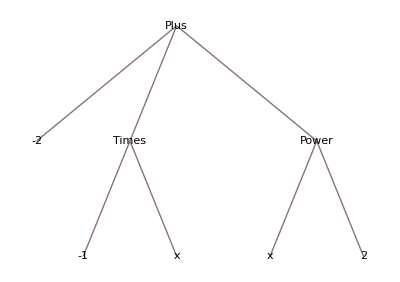

```mathematica
TreeForm[x^2-x-2]
```

### 式コピーのテクニック -- マルチプルクリック

```mathematica
Remove[f1,f2,f3,f4,y]
```

```mathematica
f1[f2[f3[f4[x]]]]
```

f1[f2[f3[f4[x]]]]

```mathematica
f1[f2[f3[f4[x,y]]]]
```

f1[f2[f3[f4[x,y]]]]

## 3.図表表示法

可視化することでデータの特徴(全体像)をとらえる。

### データの図表化

スライド:図表表示法_データの図表化.odp

#### 配列系

数表: 個体と属性の組み合わせに対して、属性値を付与する

配列表: 属性値の組に対して、個体を決定する: 周期表

相関表: 個体の組に対して、その関係を付与する

#### 座標系

属性の数が1: おもにチャートと呼ばれる: 帯グラフ、円グラフ

属性の数が2: おもにプロットと呼ばれる: 棒グラフ、折れ線グラフ

属性の数が多: 特殊グラフ: レーダーチャート、顔型グラフ

#### 連結系

要素間の関係を視覚的に連結

歴史的経過: 年表、系統樹、PERT

詳細化: 関連樹木

手続き: フローチャート

関係: グラフ(V,E)、配線図、引用関係図

#### 領域系

特に要素間の論理関係を表す

区分: 地図、クラスタリング

詳細化: シソーラス

論理関係: ベン図

### 作図

#### 配列系:配列表: [周期表]

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,118}]]
```

-Graphics-

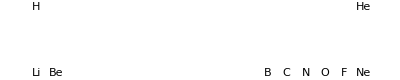

```mathematica
Graphics[Table[Text[ElementData[n,"Abbreviation"],{ElementData[n,"Group"],-ElementData[n,"Period"]}],{n,10}]]
```

2103/10/24

コードの説明:

Graphics[] -- グラフィクスオブジェクトを表示する

Text[] -- グラフィクスオブジェクト: Graphics[]内で扱えるオブジェクト

```mathematica
Graphics[a] (*エラー、表示されない*)
```

-Graphics-

```mathematica
Graphics[Text[a]] (*表示される*)
```

-Graphics-

```mathematica
Graphics[{Text[a,{0,0}],Text[b,{0,1}]}] (*座標指定による表示、複数のオブジェクトはリストでまとめる*)
```

-Graphics-

周期表の説明(スライド:周期表.odp)

ElementData[] -- 元素のデータを取得する(インターネット接続の必要アリ)

```mathematica
ElementData[8]
```

Oxygen

```mathematica
ElementData[8,"Abbreviation"]
```

O

```mathematica
ElementData[8,"Group"] (*族が数値として返ってくる*)
```

16

```mathematica
ElementData[8,"Period"] (*周期が数値として返ってくる*)
```

2

```mathematica
{ElementData[8, "Group"], -ElementData[8, "Period"]} (*周期表における座標としてデータを取り出す*)
```

{16,-2}

#### 配列系:数表:

```mathematica
TableForm[(worldShips=Sort[Cases[Map[{#,CountryData[#,"MerchantShips"]}&,CountryData[]],{_String,_Integer}],#1[[2]]>#2[[2]]&])[[{1,2,3,4,5}]],TableHeadings->{None,{"Country","Ships"}}]
```

Country | Ships
Panama | 6323
Liberia | 2204
China | 1826
Malta | 1438
Singapore | 1292

#### 配列系:数表: [ヒストグラム]

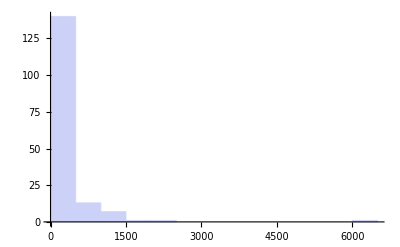

```mathematica
Histogram[Map[#[[2]]&,worldShips]]
```

#### 配列系:相関表: [隣接行列]

```mathematica
l=Range[20];
```

```mathematica
e={{1,2},{2,4},{10,12},{11,5},{12,6},{12,7},{13,6},{15,18},{16,4},{17,6}}
```

{{1,2},{2,4},{10,12},{11,5},{12,6},{12,7},{13,6},{15,18},{16,4},{17,6}}

```mathematica
Apply[UndirectedEdge,e,2]
```

{1<->2,2<->4,10<->12,11<->5,12<->6,12<->7,13<->6,15<->18,16<->4,17<->6}

```mathematica
g=Graph[l,Apply[UndirectedEdge,e,2]]
```

-Graphics-

```mathematica
AdjacencyMatrix[g]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### 座標系:棒グラフ: [ヒストグラム]

#### 座標系:折れ線グラフ:

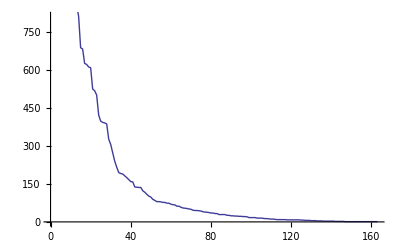

```mathematica
ListPlot[Map[#[[2]]&,worldShips],Joined->True]
```

#### 座標系:円グラフ

```mathematica
PieChart[Map[#[[2]]&,worldShips]]
```

-Graphics-

#### 座標系: [ベクトルプロット]

固有値、固有ベクトルの可視化

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

```mathematica
aDotclist = Map[a[0].# &, clist];
```

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{-3+1/2 (5+√5),1},{-3+1/2 (5-√5),1}}}

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

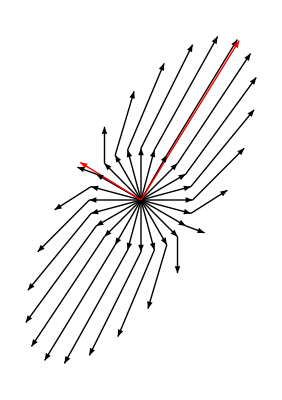

```mathematica
Show[g1, g3]
```

コードの説明:

固有値、固有ベクトルとは:
 A: 行列、x: ベクトル、λ: スカラーのとき、行列Aに対して、A.x = λ.x となる非ゼロのλ、xが求まる。
これは、行列Aによるベクトルの変換において、変換により単にλ倍されるベクトルが存在することを示す。

行列Aを次のように仮定する

```mathematica
a[0] = {{2, 1}, {1, 3}}
```

{{2,1},{1,3}}

行列によって変換されるベクトルを24個生成

```mathematica
(clist = Table[{Cos[th], Sin[th]}, {th, Pi/12, 2 Pi, Pi/12}]) // Length
```

24

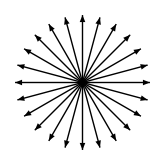

```mathematica
Graphics[Map[Arrow[{{0, 0}, #}] &, clist]]
```

24個のベクトルを行列A (a[0]) によって変換

```mathematica
aDotclist = Map[a[0].# &, clist];
```

「変換前のベクトル」と「そのベクトルの終点を始点とした変換後のベクトル」のグラフィクスオブジェクト(矢印表現)を生成

```mathematica
g1 = Graphics[{Map[Arrow[#] &, Transpose[{clist, aDotclist}]], Map[Arrow[{{0, 0}, #}] &, clist]}];
```

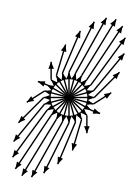

```mathematica
Graphics[g1]
```

行列A (a[0]) の固有値、固有ベクトルを求める

```mathematica
a["eigen"] = Eigensystem[a[0]]
```

{{1/2 (5+√5),1/2 (5-√5)},{{-3+1/2 (5+√5),1},{-3+1/2 (5-√5),1}}}

固有値*固有ベクトル、つまり、λ.x を求める

```mathematica
v = a["eigen"][[1]]*Map[Normalize[#] &, a["eigen"][[2]]];
```

ベクトル λ.x をグラフィクスオブジェクト(矢印表現:赤)として保存

```mathematica
g3 = Graphics[{Red, Map[Arrow[{{0, 0}, #}] &, v]}];
```

すべてのをグラフィクスオブジェクトを表示

```mathematica
Show[g1, g3]
```

-Graphics-

ベクトル {x,y} のベクトルプロット

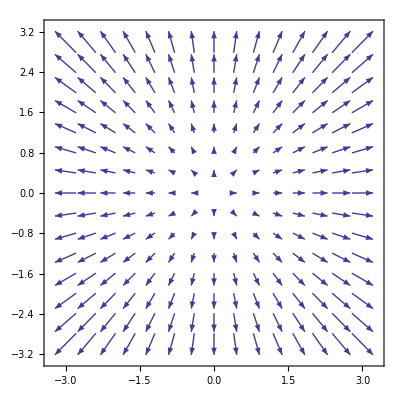

```mathematica
VectorPlot[{x, y}, {x, -3, 3}, {y, -3, 3}]
```

ベクトル {x,y} の行列 {{1,0,},{0,1}} による変換(変化無し)

```mathematica
VectorPlot[{{1,0},{0,1}}.{x, y}, {x, -3, 3}, {y, -3, 3}]
```

-Graphics-

ベクトル {x,y} の行列 {{0,1},{1,0}} による変換

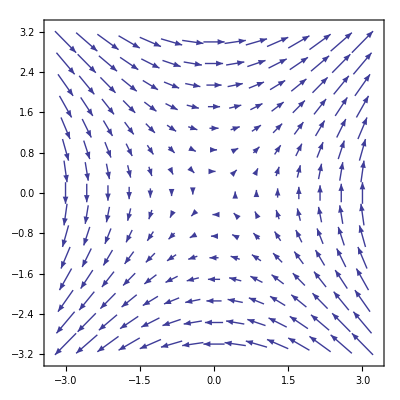

```mathematica
VectorPlot[{{0,1},{1,0}}.{x, y}, {x, -3, 3}, {y, -3, 3}]
```

ベクトル {x,y} の行列 a[0] による変換

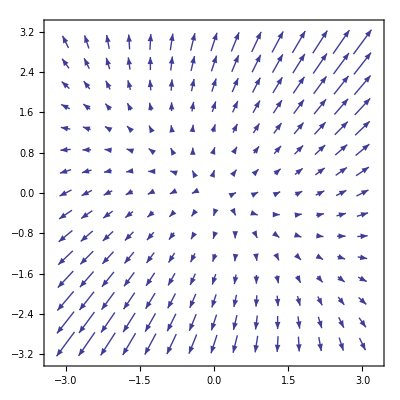

```mathematica
VectorPlot[a[0].{x, y}, {x, -3, 3}, {y, -3, 3}]
```

#### 座標系: [コンタープロット]

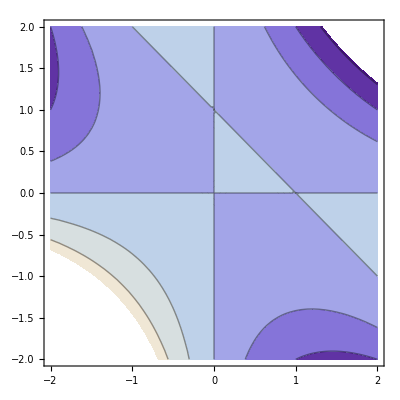

```mathematica
ContourPlot[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

#### 座標系: [3Dプロット]

```mathematica
Plot3D[x y (1-x-y),{x,-2,2},{y,-2,2}]
```

-Graphics3D-

#### 連結系:グラフ: [数式]

```mathematica
x={1,2,x}
```

{1,2,{1,2,2,{1,2,{1}}}}

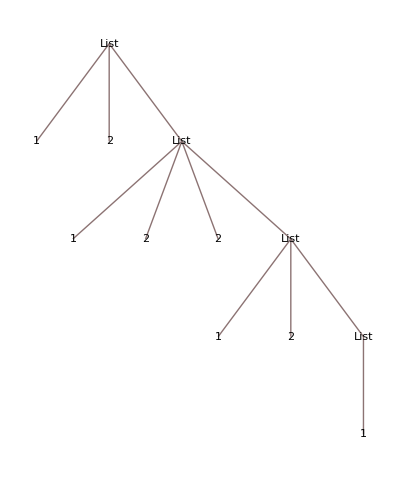

```mathematica
TreeForm[x]
```

#### 連結系:グラフ: [化学式]

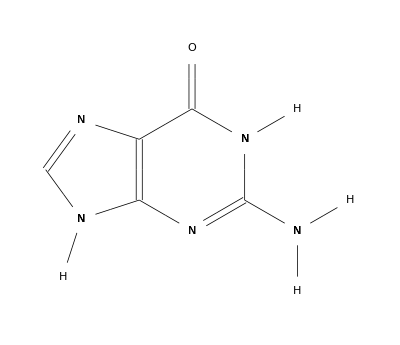

```mathematica
ChemicalData["Guanine"]
```

#### 連結系:グラフ: [崩壊図]

```mathematica
is = Select[IsotopeData[], 
   100 <= IsotopeData[#, "MassNumber"] <= 102 &];
```

```mathematica
isdata=
Map[Table[IsotopeData[#,pr],{pr,{"Symbol","DaughterNuclides"}}]&,is]
```

{{^100Kr,{Rubidium100}},{^100Rb,{Strontium100,Strontium99,Strontium98}},{^101Rb,{Strontium101,Strontium100}},{^102Rb,{Strontium102,Strontium101}},{^100Sr,{Yttrium100,Yttrium99}},{^101Sr,{Yttrium101,Yttrium100}},{^102Sr,{Yttrium102,Yttrium101}},{^100Y,{Zirconium100,Zirconium99}},{^101Y,{Zirconium101,Zirconium100}},{^102Y,{Zirconium102,Zirconium101}},{^100Zr,{Niobium100}},{^101Zr,{Niobium101}},{^102Zr,{Niobium102}},{^100Nb,{Molybdenum100}},{^101Nb,{Molybdenum101}},{^102Nb,{Molybdenum102}},{^100Mo,{Ruthenium100}},{^101Mo,{Technetium101}},{^102Mo,{Technetium102}},{^100Tc,{Ruthenium100,Molybdenum100}},{^101Tc,{Ruthenium101}},{^102Tc,{Ruthenium102}},{^100Ru,{}},{^101Ru,{}},{^102Ru,{}},{^100Rh,{Ruthenium100}},{^101Rh,{Ruthenium101}},{^102Rh,{Ruthenium102,Palladium102}},{^100Pd,{Rhodium100}},{^101Pd,{Rhodium101}},{^102Pd,{Ruthenium102}},{^100Ag,{Palladium100}},{^101Ag,{Palladium101}},{^102Ag,{Palladium102}},{^100Cd,{Silver100}},{^101Cd,{Silver101}},{^102Cd,{Silver102}},{^100In,{Cadmium100,Silver99}},{^101In,{Cadmium101,Silver100}},{^102In,{Cadmium102,Silver101}},{^100Sn,{Indium100,Cadmium99}},{^101Sn,{Indium101,Cadmium100}},{^102Sn,{Indium102,Cadmium101}}}

```mathematica
isr=Flatten[Map[Outer[List, {#[[1]]}, #[[2]]] &, isdata],2]
```

{{^100Kr,Rubidium100},{^100Rb,Strontium100},{^100Rb,Strontium99},{^100Rb,Strontium98},{^101Rb,Strontium101},{^101Rb,Strontium100},{^102Rb,Strontium102},{^102Rb,Strontium101},{^100Sr,Yttrium100},{^100Sr,Yttrium99},{^101Sr,Yttrium101},{^101Sr,Yttrium100},{^102Sr,Yttrium102},{^102Sr,Yttrium101},{^100Y,Zirconium100},{^100Y,Zirconium99},{^101Y,Zirconium101},{^101Y,Zirconium100},{^102Y,Zirconium102},{^102Y,Zirconium101},{^100Zr,Niobium100},{^101Zr,Niobium101},{^102Zr,Niobium102},{^100Nb,Molybdenum100},{^101Nb,Molybdenum101},{^102Nb,Molybdenum102},{^100Mo,Ruthenium100},{^101Mo,Technetium101},{^102Mo,Technetium102},{^100Tc,Ruthenium100},{^100Tc,Molybdenum100},{^101Tc,Ruthenium101},{^102Tc,Ruthenium102},{^100Rh,Ruthenium100},{^101Rh,Ruthenium101},{^102Rh,Ruthenium102},{^102Rh,Palladium102},{^100Pd,Rhodium100},{^101Pd,Rhodium101},{^102Pd,Ruthenium102},{^100Ag,Palladium100},{^101Ag,Palladium101},{^102Ag,Palladium102},{^100Cd,Silver100},{^101Cd,Silver101},{^102Cd,Silver102},{^100In,Cadmium100},{^100In,Silver99},{^101In,Cadmium101},{^101In,Silver100},{^102In,Cadmium102},{^102In,Silver101},{^100Sn,Indium100},{^100Sn,Cadmium99},{^101Sn,Indium101},{^101Sn,Cadmium100},{^102Sn,Indium102},{^102Sn,Cadmium101}}

```mathematica
isrl=Map[Rule[#[[1]],IsotopeData[#[[2]],"Symbol"]]&,isr]
```

{^100Kr→^100Rb,^100Rb→^100Sr,^100Rb→^99Sr,^100Rb→^98Sr,^101Rb→^101Sr,^101Rb→^100Sr,^102Rb→^102Sr,^102Rb→^101Sr,^100Sr→^100Y,^100Sr→^99Y,^101Sr→^101Y,^101Sr→^100Y,^102Sr→^102Y,^102Sr→^101Y,^100Y→^100Zr,^100Y→^99Zr,^101Y→^101Zr,^101Y→^100Zr,^102Y→^102Zr,^102Y→^101Zr,^100Zr→^100Nb,^101Zr→^101Nb,^102Zr→^102Nb,^100Nb→^100Mo,^101Nb→^101Mo,^102Nb→^102Mo,^100Mo→^100Ru,^101Mo→^101Tc,^102Mo→^102Tc,^100Tc→^100Ru,^100Tc→^100Mo,^101Tc→^101Ru,^102Tc→^102Ru,^100Rh→^100Ru,^101Rh→^101Ru,^102Rh→^102Ru,^102Rh→^102Pd,^100Pd→^100Rh,^101Pd→^101Rh,^102Pd→^102Ru,^100Ag→^100Pd,^101Ag→^101Pd,^102Ag→^102Pd,^100Cd→^100Ag,^101Cd→^101Ag,^102Cd→^102Ag,^100In→^100Cd,^100In→^99Ag,^101In→^101Cd,^101In→^100Ag,^102In→^102Cd,^102In→^101Ag,^100Sn→^100In,^100Sn→^99Cd,^101Sn→^101In,^101Sn→^100Cd,^102Sn→^102In,^102Sn→^101Cd}

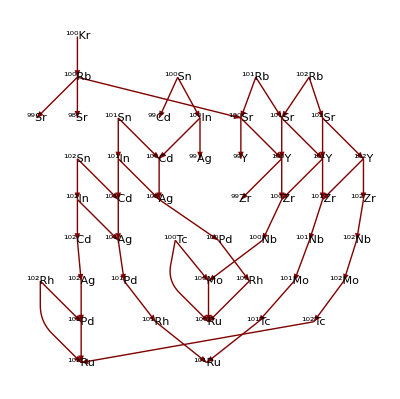

```mathematica
LayeredGraphPlot[
isrl, 
 DirectedEdges -> True, VertexLabeling -> True]
```

#### 領域系:地図: [世界地図]

いいかげんな世界地図(より正確な座標も持っている)

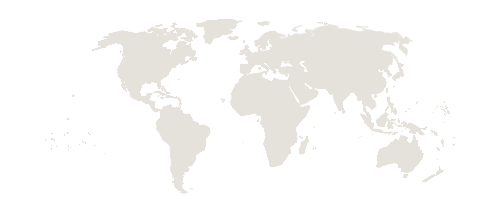

```mathematica
CountryData["World","Shape"]
```

```mathematica
coordsToXYZ[list_] := 
  Transpose[{Cos[#[[1]]]*Cos[#[[2]]], Cos[#[[1]]]*Sin[#[[2]]], 
      Sin[#[[1]]]} &@Reverse@Transpose[list*Pi/180.]];
```

```mathematica
coord3DWorld=Map[coordsToXYZ[#]&,CountryData["World","Shape"][[1]][[3]][[1]],{1}];
```

```mathematica
Graphics3D[Polygon[coord3DWorld]]
```

-Graphics3D-

#### 解析法と表示法は表裏一体(補間・スムージング)

##### 補間

```mathematica
??ListInterpolation
```

ListInterpolation[array] 与えられた値の配列を補間する近似関数を表すInterpolatingFunctionオブジェクトを作成する．
ListInterpolation[array,{{x_min,x_max},{y_min,y_max},…}] array  の各値の座標を決めるグリッド域を指定する．

Attributes[ListInterpolation]={Protected}
 
Options[ListInterpolation]={InterpolationOrder→3,Method→Automatic,PeriodicInterpolation→False}

##### 畳み込み

```mathematica
??Convolve
```

RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", StyleBox["x", "TI"], ",", StyleBox["y", "TI"]}], "]"}] 式 StyleBox["f", "TI"]と StyleBox["g", "TI"] の StyleBox["x", "TI"] についてのたたみ込みを返す．
RowBox[{"Convolve", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["g", "TI"], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["x", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["x", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["y", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["y", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] 多次元たたみ込みを返す．

Attributes[Convolve]={Protected,ReadProtected}

たたみ込みは一般に関数を滑らかにする：

```mathematica
f0=UnitBox[t0]; (*もとの関数*)
```

```mathematica
f1=Convolve[f0,f0,t0,t1] (*一回畳み込み*)
```

UnitTriangle[t1]

```mathematica
f2=Convolve[f1,f1,t1,t2] (*2回畳み込み*)
```

Piecewise[{{1/6 (4-6 t2^2-3 t2^3), -1<t2<0}, {1/6 (-6 t2-6 t2^2-t2^3), t2==-1}, {1/6 (8-12 t2+6 t2^2-t2^3), 1<t2<2}, {1/3 (2-3 t2+t2^3), t2==0}, {1/6 (6 t2-6 t2^2+t2^3), t2==1}, {1/6 (8+12 t2+6 t2^2+t2^3), -2<t2<-1}, {1/6 (4-6 t2^2+3 t2^3), 0<t2<1}, {0, True}}]

```mathematica
f3=Convolve[f2,f2,t2,t3]; (*3回畳み込み*)
```

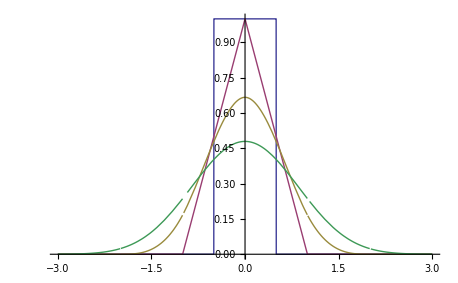

```mathematica
Plot[Evaluate[{f0,f1,f2,f3}/.{t0->x,t1->x,t2->x,t3->x}],{x,-3,3}]
```

```mathematica
Integrate[(f0/.t0->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f1/.t1->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f2/.t2->x),{x,-Infinity,Infinity}]
```

1

```mathematica
Integrate[(f3/.t3->x),{x,-Infinity,Infinity}]
```

1

```mathematica
??ListConvolve
```

ListConvolve[ker,list] 核 ker と list のたたみ込みを形成する．
ListConvolve[ker,list,k] ker の k 次の要素がlist の各要素と揃えられる循環たたみ込みを形成する．
ListConvolve[ker,list,{k_L,k_R}] 最初の要素が list[[1]] ker[[k_L]]を含み，最後の要素が list[[-1]] ker[[k_R]]を含む循環たたみ込みを形成する．
ListConvolve[ker,list,klist,p] list の最後が要素 p の反復で充填されるような，たたみ込みを形成する．
ListConvolve[ker,list,klist,{p_1,p_2,…}] list の最後が p_i で循環反復充填されるたたみ込みを形成する．
ListConvolve[ker,list,klist,padding,g,h] g がTimesの代りに，h がPlusの代りに使われる一般化されたたたみ込みを形成する．
ListConvolve[ker,list,klist,padding,g,h,lev] ker と list でレベル lev の要素を使い，たたみ込みを形成する．

Attributes[ListConvolve]={Protected}

自分自身のリスト畳み込み:

```mathematica
Partition[Array[a,10],3,1]
```

{{a[1],a[2],a[3]},{a[2],a[3],a[4]},{a[3],a[4],a[5]},{a[4],a[5],a[6]},{a[5],a[6],a[7]},{a[6],a[7],a[8]},{a[7],a[8],a[9]},{a[8],a[9],a[10]}}

```mathematica
Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[3],a[2],a[1]},{a[4],a[3],a[2]},{a[5],a[4],a[3]},{a[6],a[5],a[4]},{a[7],a[6],a[5]},{a[8],a[7],a[6]},{a[9],a[8],a[7]},{a[10],a[9],a[8]}}

```mathematica
Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]
```

{{a[1] a[3],a[2]^2,a[1] a[3]},{a[2] a[4],a[3]^2,a[2] a[4]},{a[3] a[5],a[4]^2,a[3] a[5]},{a[4] a[6],a[5]^2,a[4] a[6]},{a[5] a[7],a[6]^2,a[5] a[7]},{a[6] a[8],a[7]^2,a[6] a[8]},{a[7] a[9],a[8]^2,a[7] a[9]},{a[8] a[10],a[9]^2,a[8] a[10]}}

```mathematica
Map[Tr[#]&,Partition[Array[a,10],3,1]*Map[Reverse[#] &, Partition[Array[a, 10], 3, 1], {1}]]
```

{a[2]^2+2 a[1] a[3],a[3]^2+2 a[2] a[4],a[4]^2+2 a[3] a[5],a[5]^2+2 a[4] a[6],a[6]^2+2 a[5] a[7],a[7]^2+2 a[6] a[8],a[8]^2+2 a[7] a[9],a[9]^2+2 a[8] a[10]}

課題: 上記をひとつの関数にまとめてみよう。

2013/10/31

注意: 畳み込みは、一般的に、対象となる関数が返す値の範囲が、0 ≤ f(x) ≤ 1。
さらに、畳み込み前と畳み込み後において、マイナス無限大からプラス無限大の積分が1となるように調整できれば扱いやすい。

※畳み込みは、一種の強度 (Intensity)を取るものであり、フーリエ変換やウエーブレット変換の考えに近い。

##### 移動平均

```mathematica
??MovingAverage
```

MovingAverage[list,r] r 個の要素を平均することで計算した list の移動平均を返す．
MovingAverage[list,{w_1,w_2,…,w_r}] 重み w_i で計算した list の移動平均を返す．

Attributes[MovingAverage]={Protected,ReadProtected}

##### フィッテイング

```mathematica
??Fit
```

Fit[data,funs,vars] 変数 vars の関数 funs の線形な組合せで，与えられたデータの最小二乗法フィットを行う．

Attributes[Fit]={Protected}

```mathematica
l1=Table[n+RandomReal[{-1,1}],{n,20}]
```

{1.77847,2.40703,3.75922,3.76019,5.47608,6.01325,6.21187,7.34968,8.2711,9.14559,10.8581,12.3371,13.2659,14.1694,14.1663,16.3901,17.6836,18.8847,18.5385,20.8971}

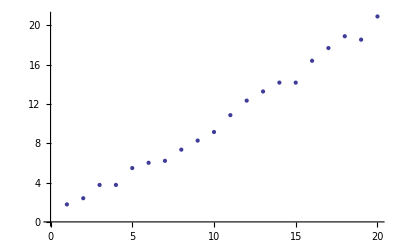

```mathematica
ListPlot[l1]
```

```mathematica
Fit[l1,{x},x]
```

1.00638 x

```mathematica
Fit[l1,{1,x},x]
```

0.004993+1.00602 x

```mathematica
Fit[l1,{1,x,x^2},x]
```

0.933295+0.752843 x+0.0120559 x^2

### 提出課題(3)

1. オシロスコープから得たデータをそのままプロットせよ

2. 1のデータを滑らかにしてプロットせよ(レンジ等に気をつけること)

## 4.探索的データ解析

より詳細にデータを見ていく。データの特徴を表す指標を考える。

### モデル

#### 準備

n次モーメント: Integrate[x^n f[x],dx] ; これは、y = f[x]としたときの、y軸に対するモーメントである。
Integrate[x^n f[x], {-Inf, +inf}, dx]は、f[x]がy軸におよぼすn次モーメントである。

n次平滑値(天野による定義、n次モーメントの値を0次モーメントの値で割ったもの): Integrate[x^n f[x],dx] / Integrate[f[x],dx]

確率分布の0次モーメントは1である。

度数分布の0次モーメント(表現がヘンだが)はサンプル総数である。

したがって、1次平滑値は平均値となる。

#### 確率密度関数 (PDF: Probability Density Function)

pdfの-無限大から+無限大までの積分が1。

すべての区間で負の値をとらない。

```mathematica
??PDF
```

PDF[dist,x] x で評価された記号分布 dist についての確率密度関数(PDF)を返す．
PDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量確率密度関数を返す．
PDF[dist] 確率密度関数を純関数として返す．

Attributes[PDF]={Protected,ReadProtected}

```mathematica
PDF[NormalDistribution[0, 1], x]
```

(ⅇ^(-x^2/2))/(√(2 π))

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

#### 累積分布関数 (CDF: Cumulative Distribution Function)

cdf(x) =∫_(-∞)^x pdf(t)ⅆt

```mathematica
??CDF
```

CDF[dist,x] x で評価された記号分布 dist の累積分布関数を返す．
CDF[dist,{x_1,x_2,…}] {x_1,x_2,…}で評価された記号分布 dist についての多変量累積分布関数を返す．
CDF[dist] CDFを純関数として返す．

Attributes[CDF]={Protected,ReadProtected}

```mathematica
CDF[NormalDistribution[0,1],x]
```

1/2 Erfc[-x/(√2)]

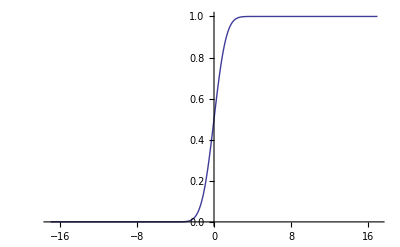

```mathematica
Plot[1/2 Erfc[-x/(√2)],{x,-16.970562748477143,16.970562748477143}]
```

#### 二重指数関数

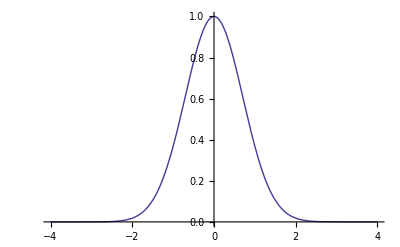

```mathematica
Plot[E^-(x^2),{x,-4,4}]
```

```mathematica
Integrate[E^-(x^2),{x,-Infinity,Infinity}]
```

√π

```mathematica
Integrate[E^-(-m+x)^2,{x,-Infinity,Infinity}]
```

√π

#### 正規分布

正規分布の式、m:平均、s:標準偏差

```mathematica
PDF[NormalDistribution[m,s], x]
```

(ⅇ^(-(-m+x)^2/(2 s^2)))/(√(2 π) s)

正規分布の形

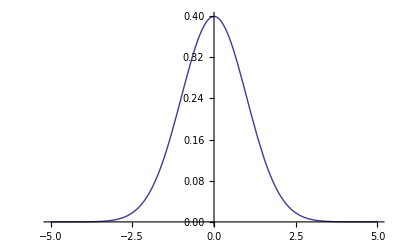

```mathematica
Plot[PDF[NormalDistribution[0,1],x],{x,-5,5}]
```

```mathematica
Integrate[PDF[NormalDistribution[0,1],x],{x,-Infinity,Infinity}]
```

1

1次モーメント / 0次モーメントは平均と一致する

```mathematica
Integrate[x PDF[NormalDistribution[m,1],x],{x,-Infinity,Infinity}]
```

m

```mathematica
Integrate[x PDF[NormalDistribution[m,4],x],{x,-Infinity,Infinity}]
```

m

度数分布の場合も同じ

```mathematica
l2={1,2,1,2,3,4,5,1,3,6}
```

{1,2,1,2,3,4,5,1,3,6}

```mathematica
Tally[l2]
```

{{1,3},{2,2},{3,2},{4,1},{5,1},{6,1}}

度数の合計 = 関数における0次モーメント

```mathematica
Map[#[[2]]&,Tally[l2]]//Tr
```

10

```mathematica
Map[#[[1]]*#[[2]]&,Tally[l2]]//Tr
```

28

度数*数値の合計 = 関数における1次モーメント

1次モーメント/0次モーメント = 平均

```mathematica
Mean[l2]
```

14/5

2次モーメントは分散と一致する(平均がゼロの場合)

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,2],x],{x,-Infinity,Infinity}]
```

4

```mathematica
Integrate[x^2 PDF[NormalDistribution[0,3],x],{x,-Infinity,Infinity}]
```

9

(x - mean(x))に対する2次モーメントは分散と一致する

```mathematica
Integrate[(x-4)^2 PDF[NormalDistribution[4,3],x],{x,-Infinity,Infinity}]
```

9

関数 CentralMoment[] は平均に対するn次モーメントを与える

```mathematica
CentralMoment[NormalDistribution[0,3],2]
```

9

```mathematica
CentralMoment[NormalDistribution[4,3],2]
```

9

正規分布の歪度(3次モーメント/2次モーメント^(3/2))は0

```mathematica
Skewness[NormalDistribution[0,1]]
```

0

正規分布の尖度(4次モーメント/2次モーメント^2)は3

```mathematica
Kurtosis[NormalDistribution[0,1]]
```

3

変曲点は、平均値±標準偏差の値と一致する

```mathematica
Solve[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

Solve::ifun: 逆関数がSolveで使われているため，求められない解がある可能性があります．解の詳細情報にはReduceをお使いください．

{{x→m-s},{x→m+s}}

```mathematica
Reduce[D[D[PDF[NormalDistribution[m,s], x],x],x]==0,{x}]
```

s≠0&&(x==m+s||x==m-s)

#### その他の分布

Zipf分布: Zipfの法則 -アイテムの出現回数とそのランクを掛けたものがほぼ一定である- に基づく

```mathematica
??ZipfDistribution
```

ZipfDistribution[ρ] 母数 ρ のゼータ分布を表す．
ZipfDistribution[n,ρ] 範囲 n のZipf分布を表す．

Attributes[ZipfDistribution]={NHoldAll,Protected,ReadProtected}

下記は、データのサイズが4の場合のランクが1から4位までの生産量比

```mathematica
PDF[ZipfDistribution[4, 1], {1, 2, 3, 4}] // N
```

{0.702439,0.17561,0.0780488,0.0439024}

図書館情報学で良く使う式は以下: zipf:生産量を返す関数、rank:ランク、a:係数、c:係数。

```mathematica
zipf[rank_,a_,c_]:=c*rank^(-a)
```

```mathematica
fitargs=FindFit[Map[#[[2]]&,worldShips],zipf[rank,a,c],{a,c},rank]
```

{a→0.929126,c→5963.12}

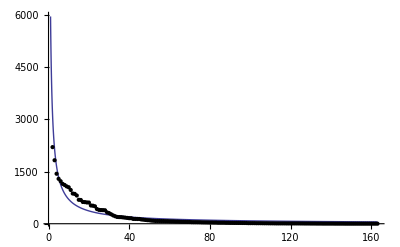

```mathematica
Plot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{#2,#1[[2]]}]]&,worldShips],PlotRange->All]
```

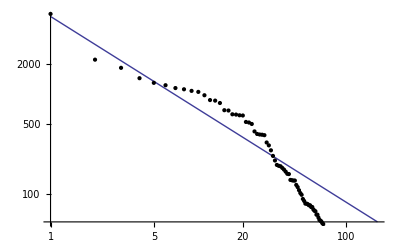

```mathematica
gobjLLP=LogLogPlot[zipf[rank,a,c]/.fitargs,{rank,1,Length[worldShips]},Epilog->MapIndexed[Point[Flatten[{Log[#2],Log[#1[[2]]]}]]&,worldShips]]
```

OrlovとChitashviliによれば、Zipf族の関数はつぎの定義のように一般化できる

```mathematica
orlovZ[m]:=Integrate[(Log[1+x]^(γ-1) x^α)/((1+x)^(m+1) (1+x)^β),{x,0,Infinity}]/Integrate[(Log[1+x]^(γ-1) x^(α-1))/((1+x)^(β+1)),{x,0,Infinity}]
```

```mathematica
orlovZ[m]
```

(∫_0^∞ x^α (1+x)^(-1-m-β) Log[1+x]^(-1+γ)ⅆx)/(∫_0^∞ x^(-1+α) (1+x)^(-1-β) Log[1+x]^(-1+γ)ⅆx)

Zipfの法則

```mathematica
orlovZ[m]/.{α->1,β->1,γ->1}
```

ConditionalExpression[1/(m+m^2),Re[m]>0]

Yuleの法則

```mathematica
orlovZ[m] /. {β -> α, γ -> 1}
```

ConditionalExpression[(α Gamma[m] Gamma[1+α])/Gamma[1+m+α],Re[α]>0&&Re[m]>0]

Yule-Simonの法則

```mathematica
orlovZ[m]/.{α->1,γ->1}
```

ConditionalExpression[β/((-1+m+β) (m+β)),Re[β]>0&&Re[m+β]>1]

### 探索的データ解析

スライド:知識構造化法_中山先生-天野改.odp

```mathematica
??Median
```

Median[list] list の要素の中央値を与える．
Median[dist] 記号分布 dist の中央値を与える．

Attributes[Median]={Protected,ReadProtected}

```mathematica
(*最頻値*)??Commonest
```

RowBox[{"Commonest", "[", StyleBox["list", "TI"], "]"}] StyleBox["list", "TI"] 中の最も一般的な要素のリストを与える．
RowBox[{"Commonest", "[", RowBox[{StyleBox["list", "TI"], ",", StyleBox["n", "TI"]}], "]"}] StyleBox["list", "TI"] 中の最も一般的な StyleBox["n", "TI"] 個の要素のリストを与える．

Attributes[Commonest]={Protected,ReadProtected}

```mathematica
??Quantile
```

Quantile[list,q] list の q 分位数を与える．
Quantile[list,{q_1,q_2,…}] 分位数 q_1, q_2, …のリストを与える．
Quantile[list,q,{{a,b},{c,d}}] パラメータ a，b，c，d で指定された分位数の定義を使う．
Quantile[dist,q] 記号分布 dist の分位数を与える．

Attributes[Quantile]={Protected,ReadProtected}

```mathematica
??BoxWhiskerChart
```

BoxWhiskerChart[{x_1,x_2,…}] 値  x_iの箱ひげ図を作成する．
BoxWhiskerChart[{x_1,x_2,…},bwspec] 記号指定 bwspec による箱ひげ図を作成する．
BoxWhiskerChart[{data_1,data_2,…},…] 各 data_iの記号による箱ひげ図を作成する．
BoxWhiskerChart[{{data_1,data_2,…},…},…] 複数のデータ集合{data_1,data_2,…}から箱ひげ図を作成する．

Attributes[BoxWhiskerChart]={Protected,ReadProtected}

#### 分布モデルとの対応

正規分布モデルプロットに対する幹葉表示

平均値に対する中央値

標準偏差に対する上下ヒンジ値、あるいは、擬似標準偏差(ヒンジ散布度を1.35で割った値)

歪度に対する中点要約値

尖度に対するヒンジ散布度(上ヒンジ値と下ヒンジ値の差)

### ランダムネス

一様乱数

```mathematica
ra=Table[Random[],{400}];
```

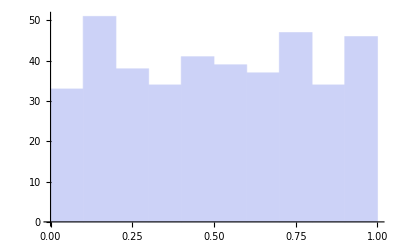

```mathematica
Histogram[ra]
```

一様乱数から分布を作る -変換法-

分布の積分の逆関数を求めることができれば、あるいは、解析的にその値を得ることができれば変換法により一様乱数から、特定の分布を得られる。

--CDFによる変換法--

```mathematica
CDF[NormalDistribution[0,1]]//FullForm
```

Function[Times[Erfc[Times[Plus[0,Times[-1,Slot[1]]],Power[Times[Sqrt[2],1],-1]]],Power[2,-1]]]

```mathematica
Plot[(1/2 Erfc[(0-#1)/(√2 1)]&)[x],{x,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
ifc:=InverseFunction[CDF[NormalDistribution[0,1]]]
```

```mathematica
ira=Map[ifc[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

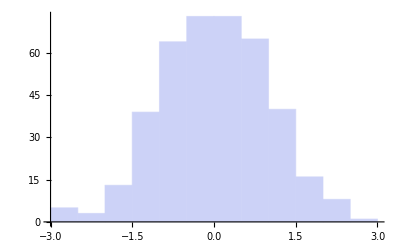

```mathematica
Histogram[ira]
```

--PDFによる変換法(積分のステップが必要)--

```mathematica
PDF[NormalDistribution[0, 1]]
```

Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&

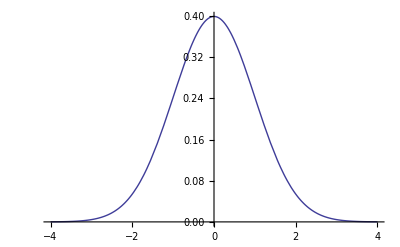

```mathematica
Plot[(Exp[-1/2 ((#1-0) 1/1)^2]/(1 √(2 π))&)[x],{x,-4,4}]
```

```mathematica
Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]
```

1/2 (1+Erf[t/(√2)])

```mathematica
Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]
```

1/2 (1+Erf[#1/(√2)])&

```mathematica
Plot[(1/2 (1+Erf[#1/(√2)])&)[x],{x,-16.970562748477143,16.970562748477143}]
```

-Graphics-

```mathematica
ifp:=InverseFunction[Function[Evaluate[Integrate[PDF[NormalDistribution[0, 1],x],{x,-Infinity,t}]/.t->#]]]
```

```mathematica
ifp[0.2]
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

-0.841621

```mathematica
ira=Map[ifp[#//N]&,ra];
```

InverseFunction::ifun: 逆関数が使用されています．値は多価逆関数のため失われている可能性があります．

General::stop: この計算中に，InverseFunction :: ifunのこれ以上の出力は表示されません．

```mathematica
ira[[1]]
```

-0.212023

```mathematica
Histogram[ira,10]
```

-Graphics-

2013/11/07

2013/11/14 : 休講

### 提出課題(4)

1. 任意のデータを取得し、適切なモデルにフィットさせよ

2. 1のデータの箱型図を作成せよ

## 5.様々な類似度・距離の考え方

データ間の関係(近さ、遠さ)を見る。

### 類似度の概念

ふたつの個体が似ていることを定義する(この関数をSとする)。

三つの個体(Va、Vb、Vc)を考える。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) > S(Va,Vc).00.00䀐

反射律: S(Va,Va) = 1 ; 完全に一致すれば1

対称律: S(Va,Vb) = S(Vb,Va) ; どちらから見ても類似度は同じ

### 非類似度の概念

ふたつの個体が似ていないことを定義する(この関数をDSとする)。

VaとVbがVaとVcより似ているなら:
S(Va,Vb) < S(Va,Vc).00.00䀐

反射律: DS(Va,Va) = 0 ; 完全に一致すれば0

対称律: DS(Va,Vb) = DS(Vb,Va) ; どちらから見ても非類似度は同じ

### 距離の概念

ふたつの個体のあいだの空間(距離)を定義する(この関数をDとする)。

VaとVbがVaとVcより近いなら:
D(Va,Vb) < D(Va,Vc).00.00䀐

反射律: D(Va,Va) = 0 ; 完全に一致すれば0

対称律: D(Va,Vb) = D(Vb,Va) ; どちらから見ても距離は同じ

推移律: D(Va,Vc) <= D(Va,Vb) + D(Vb,Vc); VaとVcの距離は、VaとVbの距離とVbとVcの距離の合計より小さい

### 個体間の距離・類似度

1変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

多変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

### 個体群間の距離・類似度(クラスタリングでは重要であるがここでは行なわない)

1変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

多変量

離散値(定性値)
-名義尺度、順序尺度

連続値(定量値)
-間隔尺度、比尺度

### 名義尺度をもとにした類似度をあらわす指標

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

m: 両方とも1

n: 両方とも0

o: {0,1}

p: {1,0}

t: アイテム数(要素数)

```mathematica
va={0,0,1,1,0}
vb={1,1,0,1,0}
```

{0,0,1,1,0}

{1,1,0,1,0}

一致係数: S(Va,Vb) = (m+n)/t

```mathematica
s[1][va_,vb_]:=Count[Map[Apply[Equal,#]&,Transpose[{va,vb}]],True]/Length[va]
```

類似比:

```mathematica
s[2][va_,vb_]:=Module[{trl,m,n,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
t=Length[trl];
m/(t-n)
]
```

```mathematica
s[2][va,vb]
```

1/4

Rogers-Tanimotoの係数:

```mathematica
s[3][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(m+n)/(t+o+p)
]
```

Hamannの係数:

```mathematica
s[4][va_,vb_]:=Module[{trl,m,n,o,p,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
n=Count[trl,{0,0}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
((m+n)-(o+p))/t
]
```

Russel-Raoの係数:

```mathematica
s[5][va_,vb_]:=Module[{trl,m,t},
trl=Transpose[{va,vb}];
m=Count[trl,{1,1}];
t=Length[trl];
m/t
]
```

ファイ係数: S(Va,Vb) = (mn - op) / ((m+o) (p+n) (m+p) (o+n))^(1/2)

2013/11/21

### 名義尺度による距離

{0,1}型データ、つまり、各カテゴリに対して1(属する)、0(属さない)の形。

不一致係数: S(Va,Vb) = (m+n)/t

```mathematica
d[1][va_,vb_]:=Module[{trl,o,p,t},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
t=Length[trl];
(o+p)/t
]
```

```mathematica
d[1][va,vb]
```

3/5

ハミング距離: S(Va,Vb) = o+p

```mathematica
d[2][va_,vb_]:=Module[{trl,o,p},
trl=Transpose[{va,vb}];
o=Count[trl,{1,0}];
p=Count[trl,{0,1}];
(o+p)
]
```

```mathematica
d[2][va,vb]
```

3

```mathematica
??HammingDistance
```

HammingDistance[u,v] 文字列またはベクトル u と v のハミング距離を返す．

Attributes[HammingDistance]={Protected}
 
Options[HammingDistance]={IgnoreCase→False}

```mathematica
HammingDistance[va,vb]
```

3

### 順序尺度をもとにした類似度

スピアマンの順位相関

```mathematica
1-6/(n^3-n) Sum[(rank[va[i]]-rank[vb[i]])^2,{i,n}]
```

1-(6 ∑_i^n (rank[va[i]]-rank[vb[i]])^2)/(-n+n^3)

```mathematica
Needs["MultivariateStatistics`"]
```

```mathematica
??SpearmanRankCorrelation
```

RowBox[{"SpearmanRankCorrelation", "[", RowBox[{StyleBox["xlist", "TI"], ",", StyleBox["ylist", "TI"]}], "]"}] 実数値ベクトル StyleBox["xlist", "TI"] と StyleBox["ylist", "TI"] に対するスピアマン(Spearman)の順位相関係数 ρ を返す．

Attributes[SpearmanRankCorrelation]={Protected}
 
SpearmanRankCorrelation[{_?NumericQ},{_?NumericQ}]:=(If[TrueQ[MultivariateStatistics`Private`$SpearmanRhoMessage],MultivariateStatistics`Private`$SpearmanRhoMessage=False;Message[General::obsfun,SpearmanRankCorrelation,SpearmanRho]];Indeterminate)
 
SpearmanRankCorrelation[MultivariateStatistics`Private`args___]:=(If[TrueQ[MultivariateStatistics`Private`$SpearmanRhoMessage],MultivariateStatistics`Private`$SpearmanRhoMessage=False;Message[General::obsfun,SpearmanRankCorrelation,SpearmanRho]];Block[{MultivariateStatistics`Private`res=MultivariateStatistics`Private`iRankCorrelation[{MultivariateStatistics`Private`args},SpearmanRankCorrelation]},MultivariateStatistics`Private`res/;MultivariateStatistics`Private`res=!=$Failed])

ケンドールの順位相関

```mathematica
??KendallRankCorrelation
```

KendallRankCorrelation[xlist,ylist] 実数値ベクトル xlist と ylist に対するケンドール(Kendall)の順位相関係数 τ を返す．

Attributes[KendallRankCorrelation]={Protected}
 
KendallRankCorrelation[{_?NumericQ},{_?NumericQ}]:=(If[TrueQ[MultivariateStatistics`Private`$KendallTauMessage],MultivariateStatistics`Private`$KendallTauMessage=False;Message[General::obsfun,KendallRankCorrelation,KendallTau]];Indeterminate)
 
KendallRankCorrelation[MultivariateStatistics`Private`args___]:=(If[TrueQ[MultivariateStatistics`Private`$KendallTauMessage],MultivariateStatistics`Private`$KendallTauMessage=False;Message[General::obsfun,KendallRankCorrelation,KendallTau]];Block[{MultivariateStatistics`Private`res=MultivariateStatistics`Private`iRankCorrelation[{MultivariateStatistics`Private`args},KendallRankCorrelation]},MultivariateStatistics`Private`res/;MultivariateStatistics`Private`res=!=$Failed])

### 定量値(間隔尺度、比率尺度)をもとにした類似度をあらわす指標

各要素は変数値

```mathematica
va={2,3,1,3,4}
vb={2,1,1,4,4}
vc=va
```

{2,3,1,3,4}

{2,1,1,4,4}

{2,3,1,3,4}

パターン類似度: S(Va,Vb) = ∑v_ai v_bi / (∑v_ai^2 v_bi^2)^(1/2)

```mathematica
s[6][va_,vb_]:=Tr[va*vb]/Sqrt[Tr[va^2]*Tr[vb^2]]
```

```mathematica
s[6][va,vb]
```

6 √(6/247)

```mathematica
s[6][va,vc]
```

1

相関係数: S(Va,Vb) = sab / (saa sbb)^(1/2) ; saa = ∑(v_ai- mean(v_a))^2 / t ; sab = ∑(v_ai - mean(v_a))(v_bi - mean(v_b)) / t

```mathematica
??Correlation
```

Correlation[v_1,v_2] ベクトル v_1とベクトル v_2の間の相関関係を返す．
Correlation[m] 行列 m の相関行列を返す．
Correlation[m_1,m_2] 行列 m_1と m_2の相関行列を返す．
Correlation[dist] 多変量記号分布 dist の相関行列を返す．
Correlation[dist,i,j] 多変量記号分布 dist の(i,j)次相関を返す．

Attributes[Correlation]={Protected,ReadProtected}

### 定量値(間隔尺度、比率尺度)をもとにした距離

ユークリッド距離: D(Va,Vb) = (∑(v_ai-v_bi)^2)^(1/2)

```mathematica
??EuclideanDistance
```

RowBox[{"EuclideanDistance", "[", RowBox[{StyleBox["u", "TI"], ",", StyleBox["v", "TI"]}], "]"}] ベクトル StyleBox["u", "TI"] と StyleBox["v", "TI"] の間のユークリッド(Euclidean)距離を返す．

Attributes[EuclideanDistance]={Protected}

重み付きユークリッド距離: D(Va,Vb) = (∑(ki(v_ai-v_bi))^2)^(1/2) ; k_i = 重み

標準化ユークリッド距離: D(Va,Vb) = (∑1/si(v_ai-v_bi)^2)^(1/2) ; si = ∑_(j=1)^N (v_ji-mean(v_i)) / N ; N =  個体数(a,bのふたつ)

市街距離(マンハッタン距離): D(Va,Vb) = ∑|v_ai-v_bi|

ミンコフスキー距離: D(Va,Vb,k) = ∑(|v_ai-v_bi|)^(1/k) ; k = 1のときマンハッタン距離、k = 2のときユークリッド距離

マハラノビスの汎距離: D(Va,Vb) = (∑∑(v_ai - v_bj)w_ij(v_aj - v_bi))^(1/2) ; w_ij = 1/(u-1)∑_(r=1)^u [(v_ri-mean(v_i))(v_rj-mean(v_j))] 、分散共分散行列の逆行列

マハラノビスの汎距離: D(Va,Vb) = Sqrt[(v_a-v_b)^Tσ^-1(v_a - v_b)] ; T:転置; σ^-1: 分散共分散行列の逆行列、サンプルの大きさ (平均と分散)を考慮(標準化)した距離。

分散共分散行列:

ベクトルxの分散は  1/N∑_(n=1)^N (x_n-mean(x))^2 と定義される。

二つのベクトルの分散または共分散を次のように定義できる。  1/N∑_(n=1)^N (x_n-mean(x))(y_x-mean(y))

```mathematica
cov[0][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/Length[x]
]
```

```mathematica
m={{1,2,3,4},{3,5,7,9}}
```

{{1,2,3,4},{3,5,7,9}}

```mathematica
m2={{1,2,3,4,5}/2,{3,4,5,6,7} 2}
```

{{1/2,1,3/2,2,5/2},{6,8,10,12,14}}

```mathematica
cov[0][m[[1]],m[[2]]]//N
```

2.5

```mathematica
cov[0][m2[[1]],m2[[2]]]//N
```

2.

分散共分散行列とは、ベクトル群の各ベクトル同士(ペアワイズ)の分散をすべて計算したもの。

```mathematica
Table[cov[0][m[[s]],m[[t]]],{s,Length[m]},{t,Length[m]}]
```

{{5/4,5/2},{5/2,5}}

```mathematica
Covariance[Transpose[m]]
```

{{5/3,10/3},{10/3,20/3}}

Mathematicaは、 Length[x]-1 で割っている。

2013/11/28

授業中課題: 分散共分散行列を返す関数

```mathematica
vCov[x_,y_]:=Table[Apply[cov[0],{x,y}[[{s,t}]]],{s,2},{t,2}]
```

```mathematica
vCov[m2[[1]],m2[[2]]]
```

{{1/2,2},{2,8}}

```mathematica
vCov[mat_]:=Outer[cov[0],mat,mat,1]
```

```mathematica
vCov[m2]
```

{{1/2,2},{2,8}}

### 文字列間(名義尺度)の距離・類似度

編集距離(レーベンシュタイン距離): 二つの文の間で、片方の文をどのように編集すれば、もう片方の文になるかのステップをカウント。

置換に関しては、1とカウントする場合と2(削除・挿入)とカウントする場合がある。

```mathematica
??EditDistance
```

EditDistance[u,v] 文字列間あるいはベクトル u と v の間の編集距離（レーベンシュタイン距離）を返す．

Attributes[EditDistance]={Protected}
 
Options[EditDistance]={IgnoreCase→False}

編集距離の拡張(ただし、反射率を満たさない)->文字列アライメントによる類似度(スライド: 5回/筑波2010_3_v1.天野改.ppt):

```mathematica
??SequenceAlignment
```

RowBox[{"SequenceAlignment", "[", RowBox[{SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]]}], "]"}] 文字列あるいはリスト SubscriptBox[StyleBox["s", "TI"], StyleBox["1", "TR"]]とリスト SubscriptBox[StyleBox["s", "TI"], StyleBox["2", "TR"]]中の一連の要素の選択的なアラインメントを求め，連続するマッチする文字列と異なる文字列を返す．

Attributes[SequenceAlignment]={Protected}
 
Options[SequenceAlignment]={GapPenalty→0,IgnoreCase→False,MergeDifferences→True,Method→Global,SimilarityRules→Automatic}

スコア行列の選択には、SimilarityRulesを使う。

```mathematica
??SimilarityRules
```

SimilarityRules SequenceAlignment等の関数のオプションで，要素ペア間で仮定する類似度スコアの規則のリストを与える．

Attributes[SimilarityRules]={Protected}

```mathematica
SequenceAlignment["ADHE","ADIE",SimilarityRules->"PAM250"]
```

{AD,{H,I},E}

類似度を求めるには別の関数を使う。

```mathematica
NeedlemanWunschSimilarity["ADHE", "ADIE",SimilarityRules->"PAM250"]
```

8.

授業中課題: 文字列アライメント(スライド: 5回/筑波2013_3_prn.pdf)

N-gramやタームのカウントによるベクトル間の距離(黒板)

### 距離行列

複数の個体間(ペアワイズ)の距離を行列で表したもの。

```mathematica
m1={1,2}
m2={3,5}
m3={5,10}
```

{1,2}

{3,5}

{5,10}

授業中課題: 上記の3つのベクトルの距離行列を求めよ。

### 提出課題(5)

長さ1000文字以上の任意の文字列を4つ以上取得し、

1. アライメント距離をもとにした距離行列と、

2. N-gramベクトルによる距離行列を求めよ。

## 5.5. 課題の提出について(NEW)

Moodleで提出

PDF、フォント埋め込み

問題を明記

データの出所を明記

結果だけでなくメソッドを明記

期限: 2013/12/15(これ以降も提出は可能、時間があれば見るが保証はない)

共著可能

4人まで(著者数による分数カウントは行なわない)

提出は個人、提出者を第一著者にすること

## 6.非階層的クラスタリング

データ間の関係からより大きな構造を見抜く。

クラスタリングとは:
そもそも分類とは、狭義には次のふたつ: 1. クラシフィケーション -あらかじめ定義されたクラスにサンプルを割り当てる- 、2. クラスタリング -クラスを動的に定義しつつ(クラスタ数も変化する)、サンプルをクラスに割り当てる- 、と理解しておけばよい。広義(ふたつを合わせたもの)には、「クラシフィケーション」=「分類」を使う。

タクソノミーとは:
生物分類法、生物分類学のこと。

クラスタリングとは、「分けること」であるが、その方法論には「分割」と「凝集」の両方の概念を含む。

### 非階層的クラスタリング

#### リーダーアルゴリズム

しきい値がある。クラスは未定。

最初の個体を最初のクラスターに入れる。

次の個体を対象にして，以下を繰り返す。個体が無くなれば終了。

最初から順にクラスターを対象にして，以下を繰り返す。

対象とする個体と，対象とするクラスターの最初の個体との距離を求める。距離がしきい値より小さければその個体を対象とするクラスタに入れ，2に戻る。

対象とする個体を新たなクラスターに登録する。.00.00䂉.00.00퀀䁸.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00ᡰ₈.05.00.00.00.00.00읕₈.04.00昁敩嵻₈䭈₇.03h62d4rv4gk81g7d3ru.03쐚ސĀ.07.00環境
設定を表示.00.00.00䎏₆ໄ₆	.00.00.00.00.00.00.00.00.00.00䁂.00.00.00.00.00䄴ￋ兑.00.00倀䂌.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00뱚4A30₣.04.00.00.00.02.00.00.00.00.00.00䀤.00.00.00.00.00멒⇩.0b湹愮㙨搲爴㑶歧ㄸ㙮礵畲.00.00.00.00.00.00.00.03쐚ތ
.00.00怀䁼.00.00䀀䂊.00.00怀䁻.00

```mathematica
list1={5,6,1,9,2,7}
```

{5,6,1,9,2,7}

例:

しきい値を3とする

最初の個体を最初のクラスターに入れる

クラスター:{{5}}        残り:{6,1,9,2,7}

残りの個体のひとつとクラスターの代表値(最初の個体)とをを次々と比べ、しきい値より近ければクラスターに加え、そうでなければ新しくクラスターを作る。新しくクラスターができたら、また、残りの個体のひとつとクラスターを比べて行く。

6 -- {5}に加える

{{5,6}}

1 -- {5,6}に加えない、新しくクラスターを作る

{{5,6},{1}}

9 -- {5,6}にも{1}にも加えない、新しくクラスターを作る

{{5,6},{1},{9}}

2 -- {1}に加える

{{5,6},{1,2},{9}}

7 -- {9}に加える

{{5,6},{1,2},{9,7}}

残りがなくなったので終了

問題: 順序により結果が変わる、逆順 -- {7,2,9,1,6,5}だと

{7,2,9,1,6,5}

最初の個体を最初のクラスターに入れる

クラスター: {{7}}      残り: {2,9,1,6,5}

2 -- 新しくクラスターを作る

{{7},{2}}   ;   {9,1,6,5}

9 -- {7} に加える

{{7,9},{2}}     ;     {1,6,5}

1 -- {2}に加える

{{7,9},{2,1}}    ;     {6,5}

6 -- {7,9}に加える

{{7,9,6},{2,1}}      ;     {5}

5 -- {7,9,6}に加える

{{7,9,6,5},{2,1}}     ;     {}

回避するにはソートする。

#### 最大距離アルゴリズム

全ての個体間の距離を求め、その最大のものを二つのクラスター中心とする。

新たなクラスター中心ができなくなるまで，以下を繰り返す。

残りの全ての個体について、全てのクラスター中心との距離を求め，最小の距離のものを取り出す。この値が、最初の距離のある一定割合（たとえば１／３）以上であるとき、対応する個体の位置を新たなクラスター中心とする。

全ての個体を最も近いクラスターに入れる。.00.00.00.00.02.00.00.00.00.00￿.00.00.00.00.00.00.00.00.00.00.00.00.0b.00ꤝ⃩.04る。.00.00.00.00.00.00.00.00ꀀ䂅.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.01.01.01.01.00.00.00떴헕￿￪.00:da88¿፠↕.04.00

```mathematica
list1
```

{5,6,1,9,2,7}

```mathematica
dmat[l_]:=Outer[EuclideanDistance,l,l]
```

```mathematica
dmat[list1]//MatrixForm
```

(0 | 1 | 4 | 4 | 3 | 2
1 | 0 | 5 | 3 | 4 | 1
4 | 5 | 0 | 8 | 1 | 6
4 | 3 | 8 | 0 | 7 | 2
3 | 4 | 1 | 7 | 0 | 5
2 | 1 | 6 | 2 | 5 | 0)

クラスター: {{1},{9}}     最初のクラスター間の距離8  しきい値3/8=0.375    残り:{5,6,2,7}

5 -- {1}との距離4、{9}との距離4 -> 新しくクラスターを作る

クラスター{{1},{9},{5}}       残り:{6,2,7}

6 -- クラスター{5}に属する

クラスター{{1},{9},{5}}       残り:{2,7}

2 -- クラスター{1}に属する

クラスター{{1},{9},{5}}       残り:{7}

7 -- クラスター{9}に属する　　　　　残り:{}

クラスターができたので、クラスター代表以外の個体を最も近いクラスターに属させる

クラスター{{1},{9},{5}}  に {6,2,7} を配分

{{1,2},{9,7},{5,6}}

リーダーアルゴリズムや最大距離法では、クラスター代表が固定される。

#### k-means(繰り返し法)

分割数kを決める。

各個体をランダムにクラスターに属させる。

各クラスターに属する個体の中心をクラスターの代表値とする。

各個体を最も近いクラスターに属させる。

3,4を繰り返すとやがて収束する。

```mathematica
list1
```

{5,6,1,9,2,7}

kを3とする

クラスターをランダムに生成:{{5,6},{1,9},{2,7}}

クラスター中心:{5.5, 8, 4.5}

各個体をもっとも近いクラスター中心をもつクラスターに属させる

```mathematica
Outer[EuclideanDistance,list1,{5.5,8,4.5}]
```

{{0.5,3,0.5},{0.5,2,1.5},{4.5,7,3.5},{3.5,1,4.5},{3.5,6,2.5},{1.5,1,2.5}}

{5,6},{9,7},{1,2}

クラスター中心{5.5, 8, 1.5}

```mathematica
Outer[EuclideanDistance,list1,{5.5,8,1.5}]
```

{{0.5,3,3.5},{0.5,2,4.5},{4.5,7,0.5},{3.5,1,7.5},{3.5,6,0.5},{1.5,1,5.5}}

{{5,6},{9,7},{1,2}}

収束した。

問題: 収束の判定をすると遅くなる。kが固定される。初期配置がランダムに決まるため同じ結果(精度)が得られない。

問題の回避: 繰り返しの複数回に一回ごとに判定。kをある範囲内で変動させることができる。

#### その他

フォギーの方法、再配置法などがあるが、k-meansに近い考え。

#### 演習

```mathematica
??FindClusters
```

FindClusters[{e_1,e_2,…}] e_i を同種の要素ごとにクラスタにまとめる．
FindClusters[{e_1->v_1,e_2->v_2,…}] 各クラスタの e_i に対応する v_i を返す．
FindClusters[{e_1,e_2,…}->{v_1,v_2,…}] 同じ結果を返す．
FindClusters[{e_1,e_2,…},n] e_i を厳密に n 個のクラスタに分割する．

Attributes[FindClusters]={Protected}
 
Options[FindClusters]={DistanceFunction→Automatic,Method→Automatic}

Method->”Optimize”にすると、前述のようなアルゴリズムが使われる(詳細は不明)。

```mathematica
??ClusteringComponents
```

ClusteringComponents[array] array の各要素がその要素が含まれるクラスタを表す整数指標で置換された配列を与える．
ClusteringComponents[array,n] 最高で n 個のクラスタを求める．
ClusteringComponents[array,n,level] array の指定レベルのクラスタを求める．
ClusteringComponents[image] image の値が同じような画素のクラスタを求める．
ClusteringComponents[image,n] image 中のクラスタを最高で n 個求める．

Attributes[ClusteringComponents]={Protected,ReadProtected}

上記3つのいずれかを関数にまとめてみよう。

### クラスタ分割の適正性の指標

#### Compactness

各クラスタがどの程度コンパクトにまとまっているか:

クラスタ中心から各メンバーへの距離の合計や平均

メンバー同士の距離の合計や平均

最大距離や最小距離を使うその他の指標

#### Separativity

各クラスタがどの程度分離できているか:

全サンプル重心から各クラスタ中心までの距離の合計や平均

クラスタ間のメンバーの距離の合計や平均

最大距離や最小距離を使うその他の指標

#### Calinski and Harabaszの指標 (Intelligent Data Analysis 12 (2008) 529–548)

値が大きいほど良い

```mathematica
(BCSM/(k-1))/(WCSM/(n-k))
```

(BCSM (-k+n))/((-1+k) WCSM)

n: 全個体数

k: クラスタ数

BCSM:

```mathematica
Sum[n[i] d[z[i],z[tot]]^2,{i,k}]
```

∑_i^k d[z[i],z[tot]]^2 n[i]

z[i] : 各クラスター中心

z[tot] : 全サンプル中心

n[i] : 各クラスタメンバー数

WCSM:

```mathematica
Sum[d[x[i,j],z[i]]^2,{i,k},{j,n[i]}]
```

∑_i^k ∑_j^n[i] d[x[i,j],z[i]]^2

x[i,j] : クラスタiのj番目のメンバー

#### Score Function (Intelligent Data Analysis 12 (2008) 529–548)

値が大きいほど良い

```mathematica
1-(1/(E^(E^(BCD-WCD))))
```

1-ⅇ^(-ⅇ^(BCD-WCD))

BCD:

```mathematica
1/(n k) Sum[n[i] d[z[i],z[tot]]^2,{i,k}]
```

(∑_i^k d[z[i],z[tot]]^2 n[i])/(k n)

n: 全個体数

k: クラスタ数

WCD:

```mathematica
1/k Sum[Sqrt[1/n[i] Sum[d[x[i,j],z[i]],{j,n[i]}]],{i,k}]
```

(∑_i^k √((∑_j^n[i] d[x[i,j],z[i]])/n[i]))/k

#### 天野の指標(オリジナル)

```mathematica
k Product[c[i]^(r[i]/r[tot]),{i,k}] (*小さいほど良い*)
```

k ∏_i^k c[i]^(r[i]/r[tot])

または、

```mathematica
1/k Product[c[i]^-(r[i]/r[tot]),{i,k}] (*大きいほど良い*)
```

(∏_i^k c[i]^(-r[i]/r[tot]))/k

r[i] : 各クラスタの平均半径

r[tot] : 全サンプルの平均半径

#### シルエット指標 (Intelligent Data Analysis 12 (2008) 529–548)

```mathematica
1/n  Sum[(b[i]-a[i])/Max[a[i],b[i]],{i,n}]
```

(∑_i^n (-a[i]+b[i])/Max[a[i],b[i]])/n

a[i] :  the average distance between point i and all other points in its own cluster

b[i] :  the minimum of the average dissimilarities(?) between i and points in other clusters

## 7.階層的クラスタリング

データ間の関係からより大きな構造(階層構造)を見抜く。

分割、もしくは、統合のルールを決めることにより、唯一のツリーを構築することができる。

個体群間の距離や類似度を定義する必要がある。

### 階層的クラスタリング(凝集法) (スライド:7回/知識構造化法_中山先生7.pptx)

#### 最短距離法

#### 最長距離法

#### 群平均法

#### 重心法

#### 演習

```mathematica
??Agglomerate
```

### 階層的クラスタリング(分裂法 - 今期やらない) (スライド:7回/知識構造化法_中山先生8.pptx)

### クラスタツリーの適正性の指標 (スライド:7回/知識構造化法_中山先生7-2.pptx)

#### コーフェン相関係数

### 階層的クラスタリング(マルチプルアライメント) (スライド: 7回/nara-wu-2_阿久津先生.ppt)

## 8.自己組織化マップ

機械学習によりデータ間の関係からより大きな構造を見抜く。

### ニューラルネットワーク

#### ニューロン

実際のニューロン:

神経細胞の構造

樹状突起: 外部や他の細胞からの刺激を受け取る

軸索: 刺激を他の細胞に伝える

細胞体: 核を保有する細胞本体

シナプス: 軸索と樹状突起の接合部、伝達する側からは神経伝達物質が放出される、伝達される側は神経伝達物質のレセプターを持つ

神経伝達のしくみ

前シナプス細胞の軸索を活動電位(インパルス)が伝わり、末端にある膨らみであるシナプス小頭に到達する

活動電位によりシナプス小頭の膜上に位置する電位依存性カルシウムイオンチャネルが開く

するとカルシウムイオンがシナプス内に流入し、シナプス小胞が細胞膜に接して神経伝達物質が細胞外に開口放出される

神経伝達物質はシナプス間隙を拡散し、後シナプス細胞の細胞膜上に分布する神経伝達物質受容体に結合する

後シナプス細胞のイオンチャネルが開き、細胞膜内外の電位差が変化する

膜に機械的、化学的、電気的刺激を受けると、膜は脱分極を起こす。約15mV程の変化、すなわち、細胞内が細胞外に比べ-55mV程になるまで脱分極すると、膜のナトリウム透過性が急激に高まり、細胞の内外の電位が逆転する（約35mV)。これを活動電位という

軸索を通じ他の細胞に刺激を伝える(興奮する)かは、同時に受け取った刺激の総和が細胞のもつしきい値を越えるかによる

活動電位が生じた部位では次にカリウムイオンが流出し、ナトリウムイオンを能動輸送によって細胞外に排出する。その結果膜の電位は一時的に-70mVよりも下がって（過分極）から静止電位に戻る。脱分極期はあらたに脱分極が起こることがないので、絶対不応期であり、過分極期は脱分極を起こしにくい状態になるので相対不応期である。そのため、一度興奮が起きた後、次の興奮が起きるまで３m秒程の不応期があることになる

活動電位が生じた部分の隣接部では軽い脱分極が起こり、新しい活動電位を生じる。これによって、興奮は次々と伝達される。これをインパルスと呼ぶ

このインパルスが軸索に到達すると、そのインパルスは軸索末端にまで到達する

神経伝達の種類

興奮性: 興奮性シナプスは信号を受け取ると、興奮性シナプス後電位（EPSP; Excitatory PostSynaptic Potential）という信号を発生させる。EPSPは神経細胞の分極状態が崩れる電位となるため、脱分極と呼ばれる。興奮性の神経伝達物質として、アセチルコリン、グルタミン酸、ノルエピネフリンなどがある。

抑制性:抑制性シナプスは信号を受け取ると、抑制性シナプス後電位（IPSP; Inhibitory PostSynaptic Potential）という信号を発生させる。IPSPは神経細胞の分極状態が強化される電位となるため、過分極と呼ばれる。抑制性の神経伝達物質にはGABA、グリシンなどがある。

シナプス前抑制性: 興奮性シナプスが起こす興奮性シナプス後電位（EPSP）を減少させる働きを持つ。

電気シナプス: 電気シナプスとは、細胞間がイオンなどを通過させる分子で接着され、細胞間に直接イオン電流が流れることによって細胞間のシグナル伝達が行われるシナプスのことを指す。化学シナプスのように方向づけられた伝達はできないが、それよりも高速な伝達が行われ、多くの細胞が協調して動作する現象を引き起こす。

計算機におけるニューロン: 実際のニューロンを忠実に真似る必要はなく自由に設計できる:

加算器

```mathematica
adder[o_List,w_List]:=Tr[w*o]
```

```mathematica
adder[{1,2,3},{a,b,c}]
```

a+2 b+3 c

入出力関数 -シグモイド関数-

```mathematica
SGM[a_,th_]:=1/(1+E^(-a+th))
```

```mathematica
Plot3D[SGM[in,th],{in,-5,5},{th,0,1},AxesLabel->Automatic]
```

-Graphics3D-

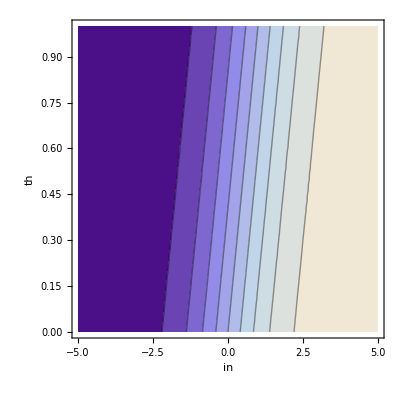

```mathematica
ContourPlot[SGM[in,th],{in,-5,5},{th,0,1},AxesLabel->Automatic]
```

ニューロンの設計

```mathematica
NER[o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
NER[1][o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],th]>=th,1,0]
```

```mathematica
NER[0][o_List,w_List,iofunc_,th_]:=If[iofunc[adder[o,w],0]>=th,1,0]
```

```mathematica
ner[o_List,w_List,iofunc_,th_]:=iofunc[adder[o,w],th]
```

加算器と入出力関数(iofunc)を組み合わせニューロンを作る。
入出力関数(iofunc)は、いま、シグモイド(0 < SGM < 1)に定義されている。
かつ、ニューロン(NER)は、非線形活性化関数として機能している。
しきい値 th は、iofunc() そのものにも影響するかたちになっている(反応を緩やかにするためで、必ずしも必要ない)。

設計したニューロンの性質:

入力を{1,1,1}、重みを{10,10,10}とする。

当然ながら、thに1より大きい値を設定すると、ニューロンの出力は、かならず 0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

当然ながら、thに0より小さい値を設定すると、ニューロンの出力は、かならず 1。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

```mathematica
Table[{NER[{1,1,1},{-10,-10,-10},SGM,th],th},{th,-0.2,1.2,0.1}]//TableForm
```

1 | -0.2
1 | -0.1
1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.
0 | 1.1
0 | 1.2

次に、重みをすべて負の値とし、thを0 <= th <= 1の間で変化させる。thが0の場合のみ、ニューロンの出力は1。

```mathematica
Table[{NER[{1,1,1},{-1,-1,-1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
0 | 0.1
0 | 0.2
0 | 0.3
0 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

重みをすべて大きな正の値とし、thを0 <= th <= 1の間で変化させる。thが1に非常に近い場合にのみ、ニューロンの出力は0。

```mathematica
Table[{NER[{1,1,1},{10,10,10},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
1 | 0.6
1 | 0.7
1 | 0.8
1 | 0.9
0 | 1.

重みを適当な値にすれば、thを0 <= th <= 1の間でニューロンの出力が決まる。

```mathematica
Table[{NER[{1,0,1},{0.,0.,0.},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
0 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

```mathematica
Table[{NER[{1,0,1},{0,0,1},SGM,th],th},{th,0,1,0.1}]//TableForm
```

1 | 0.
1 | 0.1
1 | 0.2
1 | 0.3
1 | 0.4
1 | 0.5
0 | 0.6
0 | 0.7
0 | 0.8
0 | 0.9
0 | 1.

#### 教師あり学習

ニューラルネットワークの簡単な例:

-Graphics-

学習データ: {<入力ベクトル>,<期待される出力>}

```mathematica
ldata1={
{{0,0},0},
{{1,0},0},
{{0,1},0},
{{1,1},1}
}
```

{{{0,0},0},{{1,0},0},{{0,1},0},{{1,1},1}}

```mathematica
TableForm[Map[Flatten[#]&,ldata1],TableHeadings->{Table[n,{n,4}],{"入力１","入力２","出力(期待)"}}]
```

| 入力１ | 入力２ | 出力(期待)
1 | 0 | 0 | 0
2 | 1 | 0 | 0
3 | 0 | 1 | 0
4 | 1 | 1 | 1

重みベクトル、しきい値の初期値

```mathematica
wdata[0]={1.5,-1.0}
```

{1.5,-1.}

```mathematica
thh[0]=0.8
```

0.8

```mathematica
NER[ldata1[[1,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[2,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[3,1]],wdata[0],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0

上の例では、パターン4のときに期待する値が得られていない。

学習:

重みとしきい値を変化させ、学習をおこなう。

しきい値を小さくすれば、出力は大きくなる。

```mathematica
delta=.
```

```mathematica
thh[0]
```

0.8

```mathematica
ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]
```

0.425557

```mathematica
delta[1]=ner[ldata1[[4,1]],wdata[0],SGM,thh[0]]-thh[0]
```

-0.374443

```mathematica
NER[ldata1[[4,1]],wdata[0],SGM,thh[0]+delta[1]]
```

1

入力に対応する重みを大きくすれば、出力は大きくなる。

```mathematica
wdata[0]
```

{1.5,-1.}

```mathematica
NER[ldata1[[4,1]],wdata[0]+0.5*ldata1[[4,1]],SGM,thh[0]]
```

0

```mathematica
NER[ldata1[[4,1]],wdata[0]+(0.5+0.5)*ldata1[[4,1]],SGM,thh[0]]
```

1

入力がない場合、しきい値を変化させ、入力がある場合、それに対応する重みを変化させることによって学習を行う。どの程度変化させるか -> デルタルールなど。

```mathematica
NER[ldata1[[4,1]],{1,1},SGM,0.6](*1*)
```

1

```mathematica
NER[ldata1[[3,1]],{1,1},SGM,0.6](*0*)
```

0

```mathematica
NER[ldata1[[2,1]],{1,1},SGM,0.6](*0*)
```

0

```mathematica
NER[ldata1[[1,1]],{1,1},SGM,0.6](*0*)
```

0

#### 分類機械と競合学習

分類機械:入力のパターンを出力の個数に分類する。出力の受ける入力の重みの総和は1。

-Graphics-

∑ w_i,1 = 1 ; ∑ w_i,2 = 1

競合学習の手順:

重みの初期値:

```mathematica
wmat[0]={
{0.5,0.5},
{0.6,0.4}
}
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
TableForm[wmat[0],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

入力パターン:

```mathematica
pdata1={
{1,0},
{0,1},
{1,1},
{1,0}
}
```

{{1,0},{0,1},{1,1},{1,0}}

```mathematica
TableForm[pdata1,TableHeadings->{Table[i,{i,4}],{"入力1","入力2"}}]
```

| 入力1 | 入力2
1 | 1 | 0
2 | 0 | 1
3 | 1 | 1
4 | 1 | 0

勝者に対する重みの変化量:
dw = l (c/n - w) ; l : 学習率、c : 入力値、n : 入力数、w : 現在の重み

学習係数 lを0.5に。

```mathematica
l=0.5
```

0.5

入力パターン1に対して学習:

入力パターン1の場合の出力1:

```mathematica
pdata1[[1]] wmat[0][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[1]] wmat[0][[2]]//Tr
```

0.6

出力2が勝者となる

そこで、w_2,1とw_2,2(下表)を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.6 | 0.4

```mathematica
dw[1][1,1]=0
```

0

```mathematica
dw[1][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[1,1]] : パターン1:入力1
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,1]] : パターン1:出力2、入力1のとき

```mathematica
dw[1][2,1]=l(pdata1[[1,1]]/Tr[pdata1[[1]]]-wmat[0][[2,1]])
```

0.2

つぎに、wd_2,2(出力2入力2)

pdata1[[1,2]] : パターン1:入力2
Tr[pdata1[[1]]] : パターン1:出力2への入力数
wmat[0][[2,2]] : パターン1:出力2、入力2のとき

```mathematica
dw[1][2,2]=l(pdata1[[1,2]]/Tr[pdata1[[1]]]-wmat[0][[2,2]])
```

-0.2

重みを更新:

```mathematica
wmat[0]
```

{{0.5,0.5},{0.6,0.4}}

```mathematica
wmat[1]=wmat[0]+{{dw[1][1,1],dw[1][1,2]},{dw[1][2,1],dw[1][2,2]}}
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
TableForm[wmat[1],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

入力パターン2に対して学習:

入力パターン2の場合の出力1:

```mathematica
pdata1[[2]] wmat[1][[1]]//Tr
```

0.5

入力パターン1の場合の出力2:

```mathematica
pdata1[[2]] wmat[1][[2]]//Tr
```

0.2

出力1が勝者となる

そこで、w_1,1とw_1,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

```mathematica
dw[2][2,1]=0
```

0

```mathematica
dw[2][2,2]=0
```

0

まず、wd_1,1(出力1入力1)

pdata1[[2,1]] : パターン2:入力1
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,1]] : パターン2:出力1、入力1のとき

```mathematica
dw[2][1,1]=l(pdata1[[2,1]]/Tr[pdata1[[2]]]-wmat[1][[1,1]])
```

-0.25

つぎに、wd_1,2(出力1入力2)

pdata1[[2,2]] : パターン2:入力2
Tr[pdata1[[2]]] : パターン2:出力1への入力数
wmat[1][[1,2]] : パターン2:出力1、入力2のとき

```mathematica
dw[2][1,2]=l(pdata1[[2,2]]/Tr[pdata1[[2]]]-wmat[1][[1,2]])
```

0.25

重みを更新:

```mathematica
wmat[1]
```

{{0.5,0.5},{0.8,0.2}}

```mathematica
wmat[2]=wmat[1]+{{dw[2][1,1],dw[2][1,2]},{dw[2][2,1],dw[2][2,2]}}
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
TableForm[wmat[2],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.25 | 0.75
出力2 | 0.8 | 0.2

入力パターン3に対して学習:

入力パターン3の場合の出力1:

```mathematica
pdata1[[3]] wmat[2][[1]]//Tr
```

1.

入力パターン3の場合の出力2:

```mathematica
pdata1[[3]] wmat[2][[2]]//Tr
```

1.

双方を勝者として学習させる。

そこで、w_1,1とw_1,2、w_2,1とw_2,2を変化させる。

| 入力1 | 入力2
出力1 | 0.5 | 0.5
出力2 | 0.8 | 0.2

まず、wd_1,1(出力1入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,1]] : パターン3:出力1、入力1のとき

```mathematica
dw[3][1,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[1,1]])
```

0.125

つぎに、wd_1,2(出力1入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力1への入力数
wmat[2][[1,2]] : パターン3:出力1、入力2のとき

```mathematica
dw[3][1,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[1,2]])
```

-0.125

つぎに、wd_2,1(出力2入力1)

pdata1[[3,1]] : パターン3:入力1
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,1]] : パターン3:出力2、入力1のとき

```mathematica
dw[3][2,1]=l(pdata1[[3,1]]/Tr[pdata1[[3]]]-wmat[2][[2,1]])
```

-0.15

つぎに、wd_2,2(出力2入力2)

pdata1[[3,2]] : パターン3:入力2
Tr[pdata1[[3]]] : パターン3:出力2への入力数
wmat[2][[2,2]] : パターン3:出力2、入力2のとき

```mathematica
dw[3][2,2]=l(pdata1[[3,2]]/Tr[pdata1[[3]]]-wmat[2][[2,2]])
```

0.15

重みを更新:

```mathematica
wmat[2]
```

{{0.25,0.75},{0.8,0.2}}

```mathematica
wmat[3]=wmat[2]+{{dw[3][1,1],dw[3][1,2]},{dw[3][2,1],dw[3][2,2]}}
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
TableForm[wmat[3],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

入力パターン4に対して学習:

入力パターン4の場合の出力1:

```mathematica
pdata1[[4]] wmat[3][[1]]//Tr
```

0.375

入力パターン4の場合の出力2:

```mathematica
pdata1[[4]] wmat[3][[2]]//Tr
```

0.65

出力2が勝者となる。

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.65 | 0.35

そこで、w_2,1とw_2,2を変化させる。

```mathematica
dw[4][1,1]=0
```

0

```mathematica
dw[4][1,2]=0
```

0

まず、wd_2,1(出力2入力1)

pdata1[[4,1]] : パターン4:入力1
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,1]] : パターン4:出力2、入力1のとき

```mathematica
dw[4][2,1]=l(pdata1[[4,1]]/Tr[pdata1[[4]]]-wmat[3][[2,1]])
```

0.175

つぎに、wd_2,2(出力2入力2)

pdata1[[4,2]] : パターン4:入力2
Tr[pdata1[[4]]] : パターン4:出力2への入力数
wmat[3][[2,2]] : パターン4:出力2、入力2のとき

```mathematica
dw[4][2,2]=l(pdata1[[4,2]]/Tr[pdata1[[4]]]-wmat[3][[2,2]])
```

-0.175

重みを更新:

```mathematica
wmat[3]
```

{{0.375,0.625},{0.65,0.35}}

```mathematica
wmat[4]=wmat[3]+{{dw[4][1,1],dw[4][1,2]},{dw[4][2,1],dw[4][2,2]}}
```

{{0.375,0.625},{0.825,0.175}}

```mathematica
TableForm[wmat[4],TableHeadings->{{"出力1","出力2"},{"入力1","入力2"}}]
```

| 入力1 | 入力2
出力1 | 0.375 | 0.625
出力2 | 0.825 | 0.175

学習後、分類機械として利用:

パターン1:

```mathematica
pdata1[[1]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[1]] wmat[4][[2]]//Tr
```

0.825

パターン2:

```mathematica
pdata1[[2]] wmat[4][[1]]//Tr
```

0.625

```mathematica
pdata1[[2]] wmat[4][[2]]//Tr
```

0.175

パターン3:

```mathematica
pdata1[[3]] wmat[4][[1]]//Tr
```

1.

```mathematica
pdata1[[3]] wmat[4][[2]]//Tr
```

1.

パターン4:

```mathematica
pdata1[[4]] wmat[4][[1]]//Tr
```

0.375

```mathematica
pdata1[[4]] wmat[4][[2]]//Tr
```

0.825

#### ニューラルネットワーク

ニューラルネットワークとは、以上のような、ニューロンおよびその学習の仕組みを、多階層的に組み合わせたもの。

計算機におけるニューラルネットワーク: 実際のニューラルネットワークを忠実に真似る必要はなく自由に設計できる:

実際には、良く知られている問題以外に対応するネットワーク設計は計算量の問題もあり難しい(->Deep Learning)。

設計と解法:

情報理論に基づくフィードバックモデルの作成 -> 連立常微分方程式(ODE)の定義 -> ODEを解く
常微分方程式を定義したのちに、Maple、Mathematica、Spiceなどを使う。

ネットワークモデルを直接作成する
Mathematica、Rなどに設計ツールが実装されている(Mathematicaは、さらに別パッケージを購入する必要がある)。前述の繰り返し学習による解法の実装。

### 自己組織化マップ

スライド: 知識構造化法_天野加筆9-2.pptx

## 9.主成分分析と数量化III類・IV類

データの見方を変える。

### 分散共分散

ベクトルaを仮定

```mathematica
Array[a,{3}]
```

{a[1],a[2],a[3]}

Mathematicaによる分散の計算：

```mathematica
Variance[Array[a,{3}]]
```

1/6 ((2 a[1]-a[2]-a[3]) Conjugate[a[1]]+(-a[1]+2 a[2]-a[3]) Conjugate[a[2]]+(-a[1]-a[2]+2 a[3]) Conjugate[a[3]])

分散(ベクトルaのドメインをRealに限定、ただし処理としてはインチキ)：

```mathematica
(Variance[Array[a,{3}]]//Expand)/.Conjugate[x_]->x
```

a[1]^2/3-1/3 a[1] a[2]+a[2]^2/3-1/3 a[1] a[3]-1/3 a[2] a[3]+a[3]^2/3

```mathematica
cov[1][x_,y_]:=Module[{mx,my},
mx=Mean[x];
my=Mean[y];
Tr[Map[#-mx&,x]*Map[#-my&,y]]/(Length[x]-1)
]
```

確認：Mathematicaでは(n-1)で割っている。

```mathematica
cov[1][Array[a,{3}],Array[a,{3}]]//Simplify
```

1/3 (a[1]^2+a[2]^2-a[2] a[3]+a[3]^2-a[1] (a[2]+a[3]))

```mathematica
Covariance[Array[a,3],Array[a,3]]/.Conjugate[x_]->x//Simplify
```

1/3 (a[1]^2+a[2]^2-a[2] a[3]+a[3]^2-a[1] (a[2]+a[3]))

```mathematica
??Covariance
```

Covariance[v_1,v_2] ベクトル v_1と v_2の間の共分散を返す．
Covariance[m] 行列 m の共分散行列を返す．
Covariance[m_1,m_2] 行列 m_1と m_2の共分散行列を返す．
Covariance[dist] 多変量記号分布 dist の共分散行列を返す．
Covariance[dist,i,j] 多変量記号分布 dist の(i,j)次共分散を返す．

Attributes[Covariance]={Protected,ReadProtected}
 
Options[Covariance]={}

実際のベクトルの例

```mathematica
x1={1,2,3,4}
x2={2,3,4,6}
```

{1,2,3,4}

{2,3,4,6}

```mathematica
Covariance[x1,x1]
```

13/6

```mathematica
Covariance[x1,x2]
```

13/6

```mathematica
Covariance[Transpose[{x1,x2}]]
```

{{5/3,13/6},{13/6,35/12}}

分散共分散：

```mathematica
Covariance[Array[a,{3,3}]]//MatrixForm
```

(1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,1]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,1]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,2]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,2]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,1]-a[2,1]-a[3,1]) Conjugate[a[1,3]]+(-a[1,1]+2 a[2,1]-a[3,1]) Conjugate[a[2,3]]+(-a[1,1]-a[2,1]+2 a[3,1]) Conjugate[a[3,3]])
1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,1]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,1]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,2]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,2]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,2]-a[2,2]-a[3,2]) Conjugate[a[1,3]]+(-a[1,2]+2 a[2,2]-a[3,2]) Conjugate[a[2,3]]+(-a[1,2]-a[2,2]+2 a[3,2]) Conjugate[a[3,3]])
1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,1]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,1]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,1]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,2]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,2]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,2]]) | 1/6 ((2 a[1,3]-a[2,3]-a[3,3]) Conjugate[a[1,3]]+(-a[1,3]+2 a[2,3]-a[3,3]) Conjugate[a[2,3]]+(-a[1,3]-a[2,3]+2 a[3,3]) Conjugate[a[3,3]]))

```mathematica
Covariance[Array[a,{3,3}]]/.Conjugate[x_]->x//MatrixForm
```

(1/6 (a[1,1] (2 a[1,1]-a[2,1]-a[3,1])+a[2,1] (-a[1,1]+2 a[2,1]-a[3,1])+a[3,1] (-a[1,1]-a[2,1]+2 a[3,1])) | 1/6 (a[1,2] (2 a[1,1]-a[2,1]-a[3,1])+a[2,2] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,2]) | 1/6 (a[1,3] (2 a[1,1]-a[2,1]-a[3,1])+a[2,3] (-a[1,1]+2 a[2,1]-a[3,1])+(-a[1,1]-a[2,1]+2 a[3,1]) a[3,3])
1/6 (a[1,1] (2 a[1,2]-a[2,2]-a[3,2])+a[2,1] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,1] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,2] (2 a[1,2]-a[2,2]-a[3,2])+a[2,2] (-a[1,2]+2 a[2,2]-a[3,2])+a[3,2] (-a[1,2]-a[2,2]+2 a[3,2])) | 1/6 (a[1,3] (2 a[1,2]-a[2,2]-a[3,2])+a[2,3] (-a[1,2]+2 a[2,2]-a[3,2])+(-a[1,2]-a[2,2]+2 a[3,2]) a[3,3])
1/6 (a[1,1] (2 a[1,3]-a[2,3]-a[3,3])+a[2,1] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,1] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,2] (2 a[1,3]-a[2,3]-a[3,3])+a[2,2] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,2] (-a[1,3]-a[2,3]+2 a[3,3])) | 1/6 (a[1,3] (2 a[1,3]-a[2,3]-a[3,3])+a[2,3] (-a[1,3]+2 a[2,3]-a[3,3])+a[3,3] (-a[1,3]-a[2,3]+2 a[3,3])))

### 主成分分析(PCA)

#### PCAの概念的理解(黒板)

もっとも簡単な方法は、分散共分散行列に対する固有ベクトルを求める(分散共分散法)。

```mathematica
Eigenvectors[Covariance[Array[a, {2, 2}]]]//TableForm
```

-(Conjugate[a[1,2]]-Conjugate[a[2,2]])/(Conjugate[a[1,1]]-Conjugate[a[2,1]]) | 1
-(-a[1,1]+a[2,1])/(a[1,2]-a[2,2]) | 1

実際には、さまざまな調整を含むより複雑なアルゴリズムが使われる。 -> 論文には使用したソフトウエア、バージョン、パッケージ名を記載する。

```mathematica
PrincipalComponents[Array[a,{2,2}]]//TableForm
```

((a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0
((1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])) √(a[1,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[2,1] Conjugate[a[1,1]+1/2 (-a[1,1]-a[2,1])]-a[1,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[2,1] Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]+a[1,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[2,2] Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-a[1,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]+a[2,2] Conjugate[1/2 (-a[1,2]-a[2,2])+a[2,2]]))/(√2 √(Abs[a[1,2]+1/2 (-a[1,2]-a[2,2])-((a[1,1]+1/2 (-a[1,1]-a[2,1])) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2+Abs[1/2 (-a[1,2]-a[2,2])+a[2,2]-((1/2 (-a[1,1]-a[2,1])+a[2,1]) (-Conjugate[a[1,1]]+1/2 Conjugate[a[1,1]+a[2,1]]+Conjugate[1/2 (-a[1,1]-a[2,1])+a[2,1]]))/(Conjugate[a[1,2]+1/2 (-a[1,2]-a[2,2])]-Conjugate[a[2,2]]+1/2 Conjugate[a[1,2]+a[2,2]])]^2)) | 0

#### 主成分分析による変換

##### ベクトルとマトリクスの積の処理

```mathematica
Array[k,{3,3}]
```

{{k[1,1],k[1,2],k[1,3]},{k[2,1],k[2,2],k[2,3]},{k[3,1],k[3,2],k[3,3]}}

```mathematica
Array[j,3].Array[k,{3,3}] (*縦ベクトルとして扱っている*)
```

{j[1] k[1,1]+j[2] k[2,1]+j[3] k[3,1],j[1] k[1,2]+j[2] k[2,2]+j[3] k[3,2],j[1] k[1,3]+j[2] k[2,3]+j[3] k[3,3]}

```mathematica
Array[k,{3,3}].Array[j,3]
```

{j[1] k[1,1]+j[2] k[1,2]+j[3] k[1,3],j[1] k[2,1]+j[2] k[2,2]+j[3] k[2,3],j[1] k[3,1]+j[2] k[3,2]+j[3] k[3,3]}

##### MathematicaのPCAによる変換処理を確認する( 正則行列)

```mathematica
(d={{1,2,3,5},{2,2,3,1},{5,6,2,10},{8,8,4,2}})//MatrixForm
```

(1 | 2 | 3 | 5
2 | 2 | 3 | 1
5 | 6 | 2 | 10
8 | 8 | 4 | 2)

```mathematica
(p=PrincipalComponents[d//N])//MatrixForm
```

(3.15506 | 2.3153 | 0.43005 | 0.
4.48288 | -1.50344 | -0.378729 | 0.
-4.22829 | 4.07191 | -0.202746 | 0.
-3.40966 | -4.88378 | 0.151425 | 0.)

変換mを右からかけると考えた場合:
元のデータ行列をD、PCA後の行列をPとする。Dは変換Mを経てPとなる(D.M = P)ので変換Mは、D^-1.P (= D^-1.D.M) となる。

```mathematica
d.m==p
```

```mathematica
(d^-1).d.m==m
```

```mathematica
(m=Inverse[d].p)//MatrixForm
```

(3.28523 | -0.639993 | -1.93163 | 0.
-5.10643 | 0.000807604 | 2.08979 | 0.
2.54531 | -0.339917 | -0.138114 | 0.
0.489352 | 0.794687 | -0.280713 | 0.)

```mathematica
d.m//MatrixForm (*pとおなじ*)
```

(3.15506 | 2.3153 | 0.43005 | 0.
4.48288 | -1.50344 | -0.378729 | 0.
-4.22829 | 4.07191 | -0.202746 | 0.
-3.40966 | -4.88378 | 0.151425 | 0.)

```mathematica
d[[2]].m (*mによるベクトルの変換が可能、Mathematicaは縦ベクトルとして処理*)
```

{4.48288,-1.50344,-0.378729,0.}

変換を左からかけると考えた場合:
元のデータ行列をD、PCA後の行列をPとする。Dは変換Mを経てPとなる(M.D = P)ので変換Mは、P.D^-1 (= M.D.D^-1) となる。

m.d == p

m.d.(d^-1) == m

```mathematica
(m=p.Inverse[d])//MatrixForm
```

(-1.46336 | 1.41136 | 0.623603 | -0.16529
-11.0869 | 13.8237 | 5.10061 | -4.69759
15.3863 | -20.0487 | -7.08613 | 6.98919
-2.83604 | 4.81365 | 1.36192 | -2.12631)

```mathematica
m.d//MatrixForm (*pとおなじ*)
```

(3.15506 | 2.3153 | 0.43005 | -5.55112×10^-15
4.48288 | -1.50344 | -0.378729 | 1.77636×10^-15
-4.22829 | 4.07191 | -0.202746 | -8.88178×10^-15
-3.40966 | -4.88378 | 0.151425 | 5.32907×10^-15)

```mathematica
m.d[[1]] (*第一サンプルのベクトルを取り出せない*)
```

{2.40373,8.37442,-11.0236,0.24545}

```mathematica
m.Transpose[d][[1]] (*第一成分は取り出せる*)
```

{3.15506,4.48288,-4.22829,-3.40966}

##### MathematicaのPCAによる変換処理を確認する( 正則でない行列)

```mathematica
(d={{1,2,3},{2,2,3},{5,6,2},{8,8,4}})//MatrixForm
```

(1 | 2 | 3
2 | 2 | 3
5 | 6 | 2
8 | 8 | 4)

```mathematica
(p=PrincipalComponents[d//N])//MatrixForm
```

(3.88915 | 0.144334 | 0.321964
3.16442 | 0.352642 | -0.334821
-1.68896 | -1.18165 | -0.0336485
-5.36461 | 0.684671 | 0.0465056)

変換mを右からかけると考えた場合:

```mathematica
d.m==p
```

```mathematica
Inverse[d].d.m==Inverse[d].p (*できない*)
```

```mathematica
m==(Inverse[Transpose[d].d].Transpose[d].d).m==Inverse[Transpose[d].d].Transpose[d].p(*できる*)
```

```mathematica
Inverse[Transpose[d].d].Transpose[d].p
```

{{-2.64999,0.904186,-0.208917},{1.26816,-1.01402,0.20477},{1.59098,0.329945,-0.0192689}}

### 数量化III類

```mathematica
quant3[data_]:=
 Module[{n,m,f,g,T,A,B,S,v,r,u,y,x},
  n=Length[data];
  m=Length[data[[1]]];
  f[i_]:=Apply[Plus,Table[data[[i,t]],{t,1,m}]];
  g[j_]:=Apply[Plus,Table[data[[s,j]],{s,1,n}]];
  T=Apply[Plus,Table[f[i],{i,1,n}]];
  A=N[Table[data[[t,s]]/Sqrt[g[s]],{s,1,m},{t,1,n}]];
  B=N[Table[data[[t,s]]/f[t]/Sqrt[g[s]],{t,1,n},{s,1,m}]];
  S=A.B;
  v=Eigenvalues[S];
  r=Sqrt[v];
  u=Eigenvectors[S];
  y[p_]:=Table[N[u[[p,k]] Sqrt[T]/Sqrt[g[k]]],{k,1,m}];
  x[q_]:=N[B.u[[q]] Sqrt[T]/Sqrt[v[[q]]]];
  {v,y[2],x[2]}
 ];
```

### 数量化IV類

```mathematica
quant4[nn_List]:=
 Module[{lnn, nn1, n2, zz, zz2, nn2, esnn2},
  lnn = Length[nn];
  nn1 = Table[nn[[i,j]]+nn[[j,i]],{i,lnn},{j,lnn}];
  n2 = Plus @@ nn1;
  zz = Table[0,{lnn},{lnn-1}];
  zz2 = Table[Insert[zz[[k]],-n2[[k]],k],{k,lnn}];
  nn2 = N[nn1+zz2];
  esnn2 = Eigensystem[nn2];
  {nn1, n2, zz, zz2, nn2, esnn2}
 ];
```

## 10.大規模データ解析と計算資源

大規模データの問題:

- 大規模ゆえに計算に時間がかかる

- データの保持とアクセスが難しい

### 計算資源

中央演算装置(CPU)

メインメモリー

ストレージ

外部通信装置

各装置を接続するバスやブリッジ

### コード解釈のレベル

バイナリ実行型ファイル
OS上でそのまま実行できる。

スクリプト
スクリプトを実行するプログラムが呼び出され、そのプログラムがスクリプトを解釈する(行ごとにコンパイル/実行するイメージ)。

VMコード
仮想マシンが呼び出され、仮想マシン上でコードが実行される。この限りにおいてはスクリプトファイルの実行と変わらないが、仮想マシンは万能チューリングマシンとして設計されているので、より柔軟な対応が可能となる。これにより、スクリプト言語風のプログラムコードの実行のパフォーマンスを、コンパイルされたバイナリのそれと同程度に向上させられる。一般的にソースをVM用にコンパイルして使う。

### 物理アクセス

計算資源間のコミュニケーションは、物理アクセスによって行なわれる。

例:

- CPU<->メインメモリ : 半導体(CPU、メモリー)は電源を供給され続けることによりその状態を保ち、バスの電圧変化に応じて状態を変える。

- CPU<->ストレージ間の情報伝達は直接行なわれず、一部の情報が一旦メインメモリに保持される。

情報は物理状態として保持され、情報伝達は物理アクセスによって行なわれるので、すべての情報間の距離をゼロにすることはできない。このことは、複雑だが効率のよい情報伝達システムを設計しなければならないことを意味する。

- 演算器がレジスタ(どちらもCPU内にある)の値を処理することにより演算が行なわれる。->もっとも早い計算

- 計算に必要な情報がレジスタに無い場合、CPU内キャッシュが検索される。->次に早い計算

- 計算に必要な情報が、外部キャッシュ -> メインメモリ->ストレージ、に存在する順に計算は遅くなる。

### 計算を速くするには

- 演算器と必要なデータの距離を近くする(情報の配置を最適化する) -> メインメモリ<->レジスタ間に関してコンパイラはこれをやっている。

- 考えをさらに進めて計算機資源全体をより高度な方法で管理する -> VMはこれをやっている(JITコンパイル、TAC)。

- OSそのものが近代的なVMの機能を持てば、より効率は上がると考えられる。-> 実用的なシステムはまだない。

- 計算機を寄せ集めて使う。-> 計算機クラスター。

-- 並列計算

-- 平行計算

- 現在の主流は、計算機クラスター上でコンパイルしたバイナリを使う。

### 現在の主流 -計算機クラスター + MPI + ジョブ管理システム-

アムダールの法則:
ある処理が並列化によりどの程度高速化できるかは、並列化可能な処理がどの程度含まれるかによる。

TOP500 で現在の主流を確認。

#### スレッドとプロセス

プロセスとは、OSにより認識される最小の動作(の発生と消滅の)単位。

スレッドとは、プロセス内における計算単位。プロセスをマルチスレッド化することにより複数のCPUコアを使える。

#### 計算ノード

計算ノードとは一般的にはメインメモリーを共有する単位。GPGPU、NUMA等の技術の登場により定義が曖昧になりつつあるが、MPIにおいては、メッセージパッシングが発生しない計算単位。

### Mathematica(に限らず近代的アプリケーション)は、マルチスレッド、マルチプロセス、プロセス間通信をサポートする。

## 計算メモ

-Graphics-

-Graphics-

```mathematica
data={{1,1},{-1,-1},{0.5,-0.5},{-0.5,0.5}}
```

{{1,1},{-1,-1},{0.5,-0.5},{-0.5,0.5}}

```mathematica
PrincipalComponents[data]
```

{{1.41421,2.22045×10^-16},{-1.41421,5.55112×10^-17},{0.,0.707107},{0.,-0.707107}}

```mathematica
Map[Point[#]&,PrincipalComponents[data]]//Graphics
```

-Graphics-

```mathematica
Covariance[Transpose[data]]//MatrixForm
```

(0. | 0. | 0. | 0.
0. | 0. | 0. | 0.
0. | 0. | 0.5 | -0.5
0. | 0. | -0.5 | 0.5)

```mathematica
Covariance[data]//Eigensystem
```

{{1.33333,0.333333},{{0.707107,0.707107},{-0.707107,0.707107}}}

```mathematica
es=(Covariance[Transpose[data]]//Eigensystem)
```

{{1.,5.55112×10^-16,0.,0.},{{0.,0.,-0.707107,0.707107},{0.,0.,0.707107,0.707107},{1.,0.,0.,0.},{0.,1.,0.,0.}}}

```mathematica
es[[2]]//MatrixForm
```

(0. | 0. | -0.707107 | 0.707107
0. | 0. | 0.707107 | 0.707107
1. | 0. | 0. | 0.
0. | 1. | 0. | 0.)

```mathematica
es[[1]] es[[2]]
```

{{0.,0.,-0.707107,0.707107},{0.,0.,3.92523×10^-16,3.92523×10^-16},{0.,0.,0.,0.},{0.,0.,0.,0.}}

```mathematica
es[[1]] Transpose[es[[2]]]
```

{{0.,0.,1.,0.},{0.,0.,0.,5.55112×10^-16},{0.,0.,0.,0.},{0.,0.,0.,0.}}